```mathematica
SetDirectory["D:\\Chaozhi\\GitHub Clones\\TetraOrigin\\TetraOrigin_Packages"];
Needs["TetraOrigin`"]
SetDirectory[NotebookDirectory[]]
```

D:\Chaozhi\DirectoryWUR\PolyploidProject_AFRI\TestPolyOrigin_4x\CompF1

```mathematica
calaccuracy[dataid_]:=Module[{truefile,trueval,estfile,resest,esthaplo,truehaplo,genoprob,genotypes,estorig,genorule,truegeno,truegeno2,ls,assignerr,callerr,rule,cols,esthaplo2,diff,ndoseerr,nphaseerr,nalleleerr,nparentgeno},
Print["dataid=",dataid];
truefile="F1data\\"<>dataid<>"_polyorigin_truevalue_ancestral.csv";
trueval=Import[truefile,"CSV"];
estfile="res_tetraorigin\\TetraOrigin_Output_"<>dataid<>"_LinkageGroupA_Summary.csv";
resest=getSummaryITO[estfile];
esthaplo=resest[[3]];
genoprob = resest[[-2]];
genotypes=IntegerDigits[resest[[-3]][[2;;,2]]];
genorule=Thread[genotypes->Range[Length[genotypes]]];
truegeno=Map[Sort[ToExpression[StringSplit[#,"|"]]]&,Transpose[trueval[[2;;,6;;]]],{2}];
truegeno2=truegeno/.genorule;
assignerr=1-Mean[Flatten[MapThread[#1[[#2]]&,{genoprob,truegeno2},2]]];
estorig=Map[Ordering[#,-1][[1]]&,genoprob,{2}];
ls=Flatten[truegeno2 - estorig];
callerr=1.0-Count[ls,0]/Length[ls];
truehaplo=Map[ToExpression[StringSplit[#,"|"]]&,trueval[[2;;,4;;5]],{2}];
rule=Thread[esthaplo[[1,2;;]]->Range[2,Length[esthaplo[[1]]]]];
cols = (StringTrim[#]&/@trueval[[2;;,1]])/.rule;
esthaplo2=Transpose[Transpose[#]&/@Partition[esthaplo[[3;;,cols]],4]];
diff= esthaplo2 - truehaplo;
nparentgeno = Times@@Dimensions[diff][[;;2]];
nphaseerr = nparentgeno-Count[Flatten[diff,1],Table[0,{4}]];
ndoseerr=nparentgeno-Count[Flatten[Map[Total,diff,{2}]],0];
nalleleerr=Total[Abs[Flatten[Flatten[diff,1]]]];
{ndoseerr,nphaseerr,nalleleerr,nparentgeno,assignerr,callerr}
]
```

```mathematica
reslog=ReadList["res_tetraorigin\\F1tetraorigin_log.txt"];
```

```mathematica
reslog[[;;;;3]]//MatrixForm
```

(dataid | popsize | rep | torig | tsum
F1_noff10_DR0_rep3 | 10 | 3 | 172.284 | 3.53125
F1_noff10_DR0_rep6 | 10 | 6 | 219.685 | 3.59483
F1_noff10_DR0_rep9 | 10 | 9 | 189.715 | 4.04323
F1_noff10_DR0_rep12 | 10 | 12 | 196.303 | 3.56835
F1_noff10_DR0_rep15 | 10 | 15 | 153.07 | 3.6566
F1_noff10_DR0_rep18 | 10 | 18 | 185.267 | 3.68574
F1_noff10_DR0_rep21 | 10 | 21 | 189.774 | 3.58015
F1_noff10_DR0_rep24 | 10 | 24 | 205.18 | 3.57791
F1_noff10_DR0_rep27 | 10 | 27 | 239.104 | 3.55173
F1_noff10_DR0_rep30 | 10 | 30 | 208.814 | 4.54188
F1_noff10_DR0_rep33 | 10 | 33 | 258.613 | 3.99991
F1_noff10_DR0_rep36 | 10 | 36 | 227.031 | 3.58839
F1_noff10_DR0_rep39 | 10 | 39 | 238.308 | 3.66034
F1_noff10_DR0_rep42 | 10 | 42 | 215.495 | 3.79153
F1_noff10_DR0_rep45 | 10 | 45 | 241.23 | 3.71797
F1_noff10_DR0_rep48 | 10 | 48 | 244.14 | 3.49309
F1_noff15_DR0_rep1 | 15 | 1 | 239.299 | 5.22223
F1_noff15_DR0_rep4 | 15 | 4 | 182.165 | 5.52484
F1_noff15_DR0_rep7 | 15 | 7 | 294.141 | 5.63572
F1_noff15_DR0_rep10 | 15 | 10 | 157.591 | 5.58915
F1_noff15_DR0_rep13 | 15 | 13 | 173.748 | 5.48587
F1_noff15_DR0_rep16 | 15 | 16 | 64.2841 | 5.35748
F1_noff15_DR0_rep19 | 15 | 19 | 242.122 | 5.42421
F1_noff15_DR0_rep22 | 15 | 22 | 272.557 | 5.3545
F1_noff15_DR0_rep25 | 15 | 25 | 152.469 | 5.19747
F1_noff15_DR0_rep28 | 15 | 28 | 268.631 | 5.27586
F1_noff15_DR0_rep31 | 15 | 31 | 254.928 | 5.45975
F1_noff15_DR0_rep34 | 15 | 34 | 292.814 | 5.23049
F1_noff15_DR0_rep37 | 15 | 37 | 103.174 | 5.22165
F1_noff15_DR0_rep40 | 15 | 40 | 259.388 | 5.45855
F1_noff15_DR0_rep43 | 15 | 43 | 243.87 | 5.12129
F1_noff15_DR0_rep46 | 15 | 46 | 227.899 | 5.31463
F1_noff15_DR0_rep49 | 15 | 49 | 115.117 | 5.15586
F1_noff20_DR0_rep2 | 20 | 2 | 135.273 | 7.05196
F1_noff20_DR0_rep5 | 20 | 5 | 354.682 | 7.22899
F1_noff20_DR0_rep8 | 20 | 8 | 203.703 | 6.80987
F1_noff20_DR0_rep11 | 20 | 11 | 267.078 | 6.96423
F1_noff20_DR0_rep14 | 20 | 14 | 93.9893 | 6.9346
F1_noff20_DR0_rep17 | 20 | 17 | 426.1 | 7.38692
F1_noff20_DR0_rep20 | 20 | 20 | 121.92 | 7.07123
F1_noff20_DR0_rep23 | 20 | 23 | 116.817 | 7.08093
F1_noff20_DR0_rep26 | 20 | 26 | 125.241 | 7.06998
F1_noff20_DR0_rep29 | 20 | 29 | 180.128 | 6.98868
F1_noff20_DR0_rep32 | 20 | 32 | 99.5459 | 6.77852
F1_noff20_DR0_rep35 | 20 | 35 | 83.3371 | 6.98721
F1_noff20_DR0_rep38 | 20 | 38 | 379.821 | 6.71633
F1_noff20_DR0_rep41 | 20 | 41 | 142.873 | 6.81686
F1_noff20_DR0_rep44 | 20 | 44 | 115.576 | 7.11843
F1_noff20_DR0_rep47 | 20 | 47 | 138.703 | 7.08195
F1_noff20_DR0_rep50 | 20 | 50 | 143.404 | 7.09786
F1_noff30_DR0_rep3 | 30 | 3 | 225.21 | 10.4731
F1_noff30_DR0_rep6 | 30 | 6 | 375.292 | 10.467
F1_noff30_DR0_rep9 | 30 | 9 | 92.672 | 10.2106
F1_noff30_DR0_rep12 | 30 | 12 | 93.4709 | 10.099
F1_noff30_DR0_rep15 | 30 | 15 | 193.821 | 10.4802
F1_noff30_DR0_rep18 | 30 | 18 | 315.574 | 10.3341
F1_noff30_DR0_rep21 | 30 | 21 | 206.36 | 10.9042
F1_noff30_DR0_rep24 | 30 | 24 | 272.914 | 10.6542
F1_noff30_DR0_rep27 | 30 | 27 | 100.331 | 10.4563
F1_noff30_DR0_rep30 | 30 | 30 | 146.488 | 10.442
F1_noff30_DR0_rep33 | 30 | 33 | 102.216 | 10.5031
F1_noff30_DR0_rep36 | 30 | 36 | 352.743 | 10.3276
F1_noff30_DR0_rep39 | 30 | 39 | 218.064 | 10.132
F1_noff30_DR0_rep42 | 30 | 42 | 259.876 | 10.0923
F1_noff30_DR0_rep45 | 30 | 45 | 97.8102 | 10.1534
F1_noff30_DR0_rep48 | 30 | 48 | 133.566 | 10.0202
F1_noff50_DR0_rep1 | 50 | 1 | 237.866 | 17.6191
F1_noff50_DR0_rep4 | 50 | 4 | 157.547 | 17.1809
F1_noff50_DR0_rep7 | 50 | 7 | 178.155 | 17.2653
F1_noff50_DR0_rep10 | 50 | 10 | 642.713 | 16.9963
F1_noff50_DR0_rep13 | 50 | 13 | 130.809 | 17.0828
F1_noff50_DR0_rep16 | 50 | 16 | 237.43 | 16.9435
F1_noff50_DR0_rep19 | 50 | 19 | 205.069 | 17.5127
F1_noff50_DR0_rep22 | 50 | 22 | 150.901 | 16.9736
F1_noff50_DR0_rep25 | 50 | 25 | 182.863 | 17.3363
F1_noff50_DR0_rep28 | 50 | 28 | 528.751 | 17.174
F1_noff50_DR0_rep31 | 50 | 31 | 163.472 | 17.1776
F1_noff50_DR0_rep34 | 50 | 34 | 163.314 | 16.9829
F1_noff50_DR0_rep37 | 50 | 37 | 343.433 | 16.6579
F1_noff50_DR0_rep40 | 50 | 40 | 176.435 | 17.4634
F1_noff50_DR0_rep43 | 50 | 43 | 219.14 | 17.1993
F1_noff50_DR0_rep46 | 50 | 46 | 158.314 | 16.9119
F1_noff50_DR0_rep49 | 50 | 49 | 241.413 | 16.8452
F1_noff100_DR0_rep2 | 100 | 2 | 461.467 | 35.1505
F1_noff100_DR0_rep5 | 100 | 5 | 277.616 | 32.6865
F1_noff100_DR0_rep8 | 100 | 8 | 254.227 | 32.6827
F1_noff100_DR0_rep11 | 100 | 11 | 312.439 | 32.2179
F1_noff100_DR0_rep14 | 100 | 14 | 329.672 | 31.8647
F1_noff100_DR0_rep17 | 100 | 17 | 253.741 | 32.0219
F1_noff100_DR0_rep20 | 100 | 20 | 258.566 | 32.833
F1_noff100_DR0_rep23 | 100 | 23 | 278.784 | 32.5632
F1_noff100_DR0_rep26 | 100 | 26 | 389.886 | 33.2346
F1_noff100_DR0_rep29 | 100 | 29 | 255.608 | 33.0473
F1_noff100_DR0_rep32 | 100 | 32 | 317.962 | 32.1405
F1_noff100_DR0_rep35 | 100 | 35 | 276.245 | 33.3269
F1_noff100_DR0_rep38 | 100 | 38 | 267.311 | 33.145
F1_noff100_DR0_rep41 | 100 | 41 | 347.313 | 33.4046
F1_noff100_DR0_rep44 | 100 | 44 | 410.555 | 32.3923
F1_noff100_DR0_rep47 | 100 | 47 | 299.368 | 32.548
F1_noff100_DR0_rep50 | 100 | 50 | 752.565 | 33.3975
F1_noff200_DR0_rep3 | 200 | 3 | 525.037 | 64.8139
F1_noff200_DR0_rep6 | 200 | 6 | 659.539 | 67.2992
F1_noff200_DR0_rep9 | 200 | 9 | 1496.91 | 63.7589
F1_noff200_DR0_rep12 | 200 | 12 | 659.499 | 60.5678
F1_noff200_DR0_rep15 | 200 | 15 | 734.968 | 69.789
F1_noff200_DR0_rep18 | 200 | 18 | 598.138 | 67.3639
F1_noff200_DR0_rep21 | 200 | 21 | 516.152 | 63.005
F1_noff200_DR0_rep24 | 200 | 24 | 557.547 | 69.0227
F1_noff200_DR0_rep27 | 200 | 27 | 550.346 | 71.0109
F1_noff200_DR0_rep30 | 200 | 30 | 569.652 | 72.6275
F1_noff200_DR0_rep33 | 200 | 33 | 610.31 | 72.2913
F1_noff200_DR0_rep36 | 200 | 36 | 650.844 | 71.412
F1_noff200_DR0_rep39 | 200 | 39 | 1573.65 | 70.027
F1_noff200_DR0_rep42 | 200 | 42 | 802.764 | 71.5315
F1_noff200_DR0_rep45 | 200 | 45 | 1272.61 | 65.4159
F1_noff200_DR0_rep48 | 200 | 48 | 479.831 | 66.0805
F1_noff10_DR0.5_rep1 | 10 | 1 | 235.951 | 3.15833
F1_noff10_DR0.5_rep4 | 10 | 4 | 187.765 | 3.44393
F1_noff10_DR0.5_rep7 | 10 | 7 | 230.419 | 3.42717
F1_noff10_DR0.5_rep10 | 10 | 10 | 229.048 | 3.16174
F1_noff10_DR0.5_rep13 | 10 | 13 | 209.698 | 3.2928
F1_noff10_DR0.5_rep16 | 10 | 16 | 206.838 | 3.38406
F1_noff10_DR0.5_rep19 | 10 | 19 | 229.005 | 3.79765
F1_noff10_DR0.5_rep22 | 10 | 22 | 206.339 | 3.45084
F1_noff10_DR0.5_rep25 | 10 | 25 | 200.11 | 3.25677
F1_noff10_DR0.5_rep28 | 10 | 28 | 266.27 | 3.49629
F1_noff10_DR0.5_rep31 | 10 | 31 | 230.157 | 3.30869
F1_noff10_DR0.5_rep34 | 10 | 34 | 240.228 | 4.01543
F1_noff10_DR0.5_rep37 | 10 | 37 | 202.834 | 3.36301
F1_noff10_DR0.5_rep40 | 10 | 40 | 219.612 | 3.31211
F1_noff10_DR0.5_rep43 | 10 | 43 | 237.951 | 3.41414
F1_noff10_DR0.5_rep46 | 10 | 46 | 246.838 | 3.43357
F1_noff10_DR0.5_rep49 | 10 | 49 | 268.933 | 3.9691
F1_noff15_DR0.5_rep2 | 15 | 2 | 385.165 | 4.84477
F1_noff15_DR0.5_rep5 | 15 | 5 | 326.555 | 5.26292
F1_noff15_DR0.5_rep8 | 15 | 8 | 228.273 | 4.79145
F1_noff15_DR0.5_rep11 | 15 | 11 | 309.368 | 4.73602
F1_noff15_DR0.5_rep14 | 15 | 14 | 321.749 | 4.91567
F1_noff15_DR0.5_rep17 | 15 | 17 | 215.603 | 4.39076
F1_noff15_DR0.5_rep20 | 15 | 20 | 241.47 | 4.48773
F1_noff15_DR0.5_rep23 | 15 | 23 | 232.661 | 4.46373
F1_noff15_DR0.5_rep26 | 15 | 26 | 228.391 | 4.55305
F1_noff15_DR0.5_rep29 | 15 | 29 | 262.381 | 4.8669
F1_noff15_DR0.5_rep32 | 15 | 32 | 252.392 | 4.55906
F1_noff15_DR0.5_rep35 | 15 | 35 | 216.843 | 4.48188
F1_noff15_DR0.5_rep38 | 15 | 38 | 234.59 | 4.69749
F1_noff15_DR0.5_rep41 | 15 | 41 | 278.966 | 4.60332
F1_noff15_DR0.5_rep44 | 15 | 44 | 297.889 | 4.54163
F1_noff15_DR0.5_rep47 | 15 | 47 | 221.904 | 4.45729
F1_noff15_DR0.5_rep50 | 15 | 50 | 283.439 | 4.76882
F1_noff20_DR0.5_rep3 | 20 | 3 | 327.833 | 6.02153
F1_noff20_DR0.5_rep6 | 20 | 6 | 299.119 | 6.06879
F1_noff20_DR0.5_rep9 | 20 | 9 | 293.587 | 6.22009
F1_noff20_DR0.5_rep12 | 20 | 12 | 322.905 | 5.91845
F1_noff20_DR0.5_rep15 | 20 | 15 | 336.958 | 5.99929
F1_noff20_DR0.5_rep18 | 20 | 18 | 227.71 | 5.82037
F1_noff20_DR0.5_rep21 | 20 | 21 | 229.774 | 5.77874
F1_noff20_DR0.5_rep24 | 20 | 24 | 90.3802 | 5.80677
F1_noff20_DR0.5_rep27 | 20 | 27 | 308.039 | 6.04665
F1_noff20_DR0.5_rep30 | 20 | 30 | 294.916 | 5.751
F1_noff20_DR0.5_rep33 | 20 | 33 | 136.696 | 6.1639
F1_noff20_DR0.5_rep36 | 20 | 36 | 245.946 | 5.28694
F1_noff20_DR0.5_rep39 | 20 | 39 | 106.505 | 5.29669
F1_noff20_DR0.5_rep42 | 20 | 42 | 123.547 | 5.48708
F1_noff20_DR0.5_rep45 | 20 | 45 | 91.364 | 5.38411
F1_noff20_DR0.5_rep48 | 20 | 48 | 256.662 | 5.46683
F1_noff30_DR0.5_rep1 | 30 | 1 | 223.524 | 8.02417
F1_noff30_DR0.5_rep4 | 30 | 4 | 265.412 | 7.91611
F1_noff30_DR0.5_rep7 | 30 | 7 | 105.757 | 7.9185
F1_noff30_DR0.5_rep10 | 30 | 10 | 214.57 | 7.78521
F1_noff30_DR0.5_rep13 | 30 | 13 | 130. | 7.94043
F1_noff30_DR0.5_rep16 | 30 | 16 | 105.78 | 7.68816
F1_noff30_DR0.5_rep19 | 30 | 19 | 147.934 | 7.72035
F1_noff30_DR0.5_rep22 | 30 | 22 | 138.537 | 8.03218
F1_noff30_DR0.5_rep25 | 30 | 25 | 102.708 | 8.01633
F1_noff30_DR0.5_rep28 | 30 | 28 | 275.017 | 7.86656
F1_noff30_DR0.5_rep31 | 30 | 31 | 201.318 | 7.85358
F1_noff30_DR0.5_rep34 | 30 | 34 | 90.1623 | 7.67234
F1_noff30_DR0.5_rep37 | 30 | 37 | 392.35 | 7.80274
F1_noff30_DR0.5_rep40 | 30 | 40 | 346.555 | 8.03352
F1_noff30_DR0.5_rep43 | 30 | 43 | 299.118 | 7.89177
F1_noff30_DR0.5_rep46 | 30 | 46 | 197.576 | 7.93795
F1_noff30_DR0.5_rep49 | 30 | 49 | 136.976 | 7.8913
F1_noff50_DR0.5_rep2 | 50 | 2 | 263.635 | 13.0535
F1_noff50_DR0.5_rep5 | 50 | 5 | 138.996 | 12.961
F1_noff50_DR0.5_rep8 | 50 | 8 | 364.213 | 12.9238
F1_noff50_DR0.5_rep11 | 50 | 11 | 201.445 | 12.9411
F1_noff50_DR0.5_rep14 | 50 | 14 | 141.786 | 12.9678
F1_noff50_DR0.5_rep17 | 50 | 17 | 201.955 | 13.3145
F1_noff50_DR0.5_rep20 | 50 | 20 | 146.474 | 14.3772
F1_noff50_DR0.5_rep23 | 50 | 23 | 237.18 | 13.2468
F1_noff50_DR0.5_rep26 | 50 | 26 | 219.773 | 13.4968
F1_noff50_DR0.5_rep29 | 50 | 29 | 253.705 | 14.3566
F1_noff50_DR0.5_rep32 | 50 | 32 | 238.496 | 14.888
F1_noff50_DR0.5_rep35 | 50 | 35 | 146.66 | 15.0386
F1_noff50_DR0.5_rep38 | 50 | 38 | 183.224 | 14.9816
F1_noff50_DR0.5_rep41 | 50 | 41 | 410.713 | 14.6952
F1_noff50_DR0.5_rep44 | 50 | 44 | 377.138 | 13.5855
F1_noff50_DR0.5_rep47 | 50 | 47 | 261.198 | 14.231
F1_noff50_DR0.5_rep50 | 50 | 50 | 138.066 | 14.33
F1_noff100_DR0.5_rep3 | 100 | 3 | 229.48 | 29.9482
F1_noff100_DR0.5_rep6 | 100 | 6 | 226.95 | 29.8368
F1_noff100_DR0.5_rep9 | 100 | 9 | 288.111 | 28.7192
F1_noff100_DR0.5_rep12 | 100 | 12 | 238.547 | 28.493
F1_noff100_DR0.5_rep15 | 100 | 15 | 251.476 | 29.5816
F1_noff100_DR0.5_rep18 | 100 | 18 | 329.777 | 29.3125
F1_noff100_DR0.5_rep21 | 100 | 21 | 497.165 | 28.8419
F1_noff100_DR0.5_rep24 | 100 | 24 | 247.234 | 29.1975
F1_noff100_DR0.5_rep27 | 100 | 27 | 690.588 | 27.5448
F1_noff100_DR0.5_rep30 | 100 | 30 | 234.323 | 26.8582
F1_noff100_DR0.5_rep33 | 100 | 33 | 268.161 | 27.5579
F1_noff100_DR0.5_rep36 | 100 | 36 | 256.175 | 28.2421
F1_noff100_DR0.5_rep39 | 100 | 39 | 656.207 | 28.239
F1_noff100_DR0.5_rep42 | 100 | 42 | 308.93 | 29.1272
F1_noff100_DR0.5_rep45 | 100 | 45 | 260.077 | 28.9242
F1_noff100_DR0.5_rep48 | 100 | 48 | 279.735 | 28.5752
F1_noff200_DR0.5_rep1 | 200 | 1 | 1363.94 | 57.3165
F1_noff200_DR0.5_rep4 | 200 | 4 | 1413.61 | 57.7121
F1_noff200_DR0.5_rep7 | 200 | 7 | 508.411 | 56.4715
F1_noff200_DR0.5_rep10 | 200 | 10 | 731.789 | 56.6042
F1_noff200_DR0.5_rep13 | 200 | 13 | 472.453 | 57.6471
F1_noff200_DR0.5_rep16 | 200 | 16 | 1441.49 | 56.4432
F1_noff200_DR0.5_rep19 | 200 | 19 | 571.944 | 57.7766
F1_noff200_DR0.5_rep22 | 200 | 22 | 1792.4 | 66.8234
F1_noff200_DR0.5_rep25 | 200 | 25 | 926.996 | 71.7971
F1_noff200_DR0.5_rep28 | 200 | 28 | 584.118 | 61.2827
F1_noff200_DR0.5_rep31 | 200 | 31 | 868.639 | 60.1035
F1_noff200_DR0.5_rep34 | 200 | 34 | 608.414 | 60.1661
F1_noff200_DR0.5_rep37 | 200 | 37 | 1589.65 | 61.1586
F1_noff200_DR0.5_rep40 | 200 | 40 | 771.939 | 61.4842
F1_noff200_DR0.5_rep43 | 200 | 43 | 1374.03 | 58.6491
F1_noff200_DR0.5_rep46 | 200 | 46 | 457.444 | 57.6759
F1_noff200_DR0.5_rep49 | 200 | 49 | 487.695 | 57.9964)

```mathematica
calaccuracy[reslog[[2,1]]]
```

dataid=F1_noff10_DR0_rep1

{5,21,50,402,0.13211,0.112438}

```mathematica
reslog=ReadList["res_tetraorigin\\F1tetraorigin_log.txt"];
acc=calaccuracy[#]&/@reslog[[2;;,1]];//AbsoluteTiming
acc2=Join[{{"ndoseerr","nphaseerr","nalleleerr","nparentgeno","assignerr","callerr"}},acc];
ressum = Join[reslog,acc2,2];
```

dataid=F1_noff10_DR0_rep1

dataid=F1_noff10_DR0_rep2

dataid=F1_noff10_DR0_rep3

dataid=F1_noff10_DR0_rep4

dataid=F1_noff10_DR0_rep5

dataid=F1_noff10_DR0_rep6

dataid=F1_noff10_DR0_rep7

dataid=F1_noff10_DR0_rep8

dataid=F1_noff10_DR0_rep9

dataid=F1_noff10_DR0_rep10

dataid=F1_noff10_DR0_rep11

dataid=F1_noff10_DR0_rep12

dataid=F1_noff10_DR0_rep13

dataid=F1_noff10_DR0_rep14

dataid=F1_noff10_DR0_rep15

dataid=F1_noff10_DR0_rep16

dataid=F1_noff10_DR0_rep17

dataid=F1_noff10_DR0_rep18

dataid=F1_noff10_DR0_rep19

dataid=F1_noff10_DR0_rep20

dataid=F1_noff10_DR0_rep21

dataid=F1_noff10_DR0_rep22

dataid=F1_noff10_DR0_rep23

dataid=F1_noff10_DR0_rep24

dataid=F1_noff10_DR0_rep25

dataid=F1_noff10_DR0_rep26

dataid=F1_noff10_DR0_rep27

dataid=F1_noff10_DR0_rep28

dataid=F1_noff10_DR0_rep29

dataid=F1_noff10_DR0_rep30

dataid=F1_noff10_DR0_rep31

dataid=F1_noff10_DR0_rep32

dataid=F1_noff10_DR0_rep33

dataid=F1_noff10_DR0_rep34

dataid=F1_noff10_DR0_rep35

dataid=F1_noff10_DR0_rep36

dataid=F1_noff10_DR0_rep37

dataid=F1_noff10_DR0_rep38

dataid=F1_noff10_DR0_rep39

dataid=F1_noff10_DR0_rep40

dataid=F1_noff10_DR0_rep41

dataid=F1_noff10_DR0_rep42

dataid=F1_noff10_DR0_rep43

dataid=F1_noff10_DR0_rep44

dataid=F1_noff10_DR0_rep45

dataid=F1_noff10_DR0_rep46

dataid=F1_noff10_DR0_rep47

dataid=F1_noff10_DR0_rep48

dataid=F1_noff10_DR0_rep49

dataid=F1_noff10_DR0_rep50

dataid=F1_noff15_DR0_rep1

dataid=F1_noff15_DR0_rep2

dataid=F1_noff15_DR0_rep3

dataid=F1_noff15_DR0_rep4

dataid=F1_noff15_DR0_rep5

dataid=F1_noff15_DR0_rep6

dataid=F1_noff15_DR0_rep7

dataid=F1_noff15_DR0_rep8

dataid=F1_noff15_DR0_rep9

dataid=F1_noff15_DR0_rep10

dataid=F1_noff15_DR0_rep11

dataid=F1_noff15_DR0_rep12

dataid=F1_noff15_DR0_rep13

dataid=F1_noff15_DR0_rep14

dataid=F1_noff15_DR0_rep15

dataid=F1_noff15_DR0_rep16

dataid=F1_noff15_DR0_rep17

dataid=F1_noff15_DR0_rep18

dataid=F1_noff15_DR0_rep19

dataid=F1_noff15_DR0_rep20

dataid=F1_noff15_DR0_rep21

dataid=F1_noff15_DR0_rep22

dataid=F1_noff15_DR0_rep23

dataid=F1_noff15_DR0_rep24

dataid=F1_noff15_DR0_rep25

dataid=F1_noff15_DR0_rep26

dataid=F1_noff15_DR0_rep27

dataid=F1_noff15_DR0_rep28

dataid=F1_noff15_DR0_rep29

dataid=F1_noff15_DR0_rep30

dataid=F1_noff15_DR0_rep31

dataid=F1_noff15_DR0_rep32

dataid=F1_noff15_DR0_rep33

dataid=F1_noff15_DR0_rep34

dataid=F1_noff15_DR0_rep35

dataid=F1_noff15_DR0_rep36

dataid=F1_noff15_DR0_rep37

dataid=F1_noff15_DR0_rep38

dataid=F1_noff15_DR0_rep39

dataid=F1_noff15_DR0_rep40

dataid=F1_noff15_DR0_rep41

dataid=F1_noff15_DR0_rep42

dataid=F1_noff15_DR0_rep43

dataid=F1_noff15_DR0_rep44

dataid=F1_noff15_DR0_rep45

dataid=F1_noff15_DR0_rep46

dataid=F1_noff15_DR0_rep47

dataid=F1_noff15_DR0_rep48

dataid=F1_noff15_DR0_rep49

dataid=F1_noff15_DR0_rep50

dataid=F1_noff20_DR0_rep1

dataid=F1_noff20_DR0_rep2

dataid=F1_noff20_DR0_rep3

dataid=F1_noff20_DR0_rep4

dataid=F1_noff20_DR0_rep5

dataid=F1_noff20_DR0_rep6

dataid=F1_noff20_DR0_rep7

dataid=F1_noff20_DR0_rep8

dataid=F1_noff20_DR0_rep9

dataid=F1_noff20_DR0_rep10

dataid=F1_noff20_DR0_rep11

dataid=F1_noff20_DR0_rep12

dataid=F1_noff20_DR0_rep13

dataid=F1_noff20_DR0_rep14

dataid=F1_noff20_DR0_rep15

dataid=F1_noff20_DR0_rep16

dataid=F1_noff20_DR0_rep17

dataid=F1_noff20_DR0_rep18

dataid=F1_noff20_DR0_rep19

dataid=F1_noff20_DR0_rep20

dataid=F1_noff20_DR0_rep21

dataid=F1_noff20_DR0_rep22

dataid=F1_noff20_DR0_rep23

dataid=F1_noff20_DR0_rep24

dataid=F1_noff20_DR0_rep25

dataid=F1_noff20_DR0_rep26

dataid=F1_noff20_DR0_rep27

dataid=F1_noff20_DR0_rep28

dataid=F1_noff20_DR0_rep29

dataid=F1_noff20_DR0_rep30

dataid=F1_noff20_DR0_rep31

dataid=F1_noff20_DR0_rep32

dataid=F1_noff20_DR0_rep33

dataid=F1_noff20_DR0_rep34

dataid=F1_noff20_DR0_rep35

dataid=F1_noff20_DR0_rep36

dataid=F1_noff20_DR0_rep37

dataid=F1_noff20_DR0_rep38

dataid=F1_noff20_DR0_rep39

dataid=F1_noff20_DR0_rep40

dataid=F1_noff20_DR0_rep41

dataid=F1_noff20_DR0_rep42

dataid=F1_noff20_DR0_rep43

dataid=F1_noff20_DR0_rep44

dataid=F1_noff20_DR0_rep45

dataid=F1_noff20_DR0_rep46

dataid=F1_noff20_DR0_rep47

dataid=F1_noff20_DR0_rep48

dataid=F1_noff20_DR0_rep49

dataid=F1_noff20_DR0_rep50

dataid=F1_noff30_DR0_rep1

dataid=F1_noff30_DR0_rep2

dataid=F1_noff30_DR0_rep3

dataid=F1_noff30_DR0_rep4

dataid=F1_noff30_DR0_rep5

dataid=F1_noff30_DR0_rep6

dataid=F1_noff30_DR0_rep7

dataid=F1_noff30_DR0_rep8

dataid=F1_noff30_DR0_rep9

dataid=F1_noff30_DR0_rep10

dataid=F1_noff30_DR0_rep11

dataid=F1_noff30_DR0_rep12

dataid=F1_noff30_DR0_rep13

dataid=F1_noff30_DR0_rep14

dataid=F1_noff30_DR0_rep15

dataid=F1_noff30_DR0_rep16

dataid=F1_noff30_DR0_rep17

dataid=F1_noff30_DR0_rep18

dataid=F1_noff30_DR0_rep19

dataid=F1_noff30_DR0_rep20

dataid=F1_noff30_DR0_rep21

dataid=F1_noff30_DR0_rep22

dataid=F1_noff30_DR0_rep23

dataid=F1_noff30_DR0_rep24

dataid=F1_noff30_DR0_rep25

dataid=F1_noff30_DR0_rep26

dataid=F1_noff30_DR0_rep27

dataid=F1_noff30_DR0_rep28

dataid=F1_noff30_DR0_rep29

dataid=F1_noff30_DR0_rep30

dataid=F1_noff30_DR0_rep31

dataid=F1_noff30_DR0_rep32

dataid=F1_noff30_DR0_rep33

dataid=F1_noff30_DR0_rep34

dataid=F1_noff30_DR0_rep35

dataid=F1_noff30_DR0_rep36

dataid=F1_noff30_DR0_rep37

dataid=F1_noff30_DR0_rep38

dataid=F1_noff30_DR0_rep39

dataid=F1_noff30_DR0_rep40

dataid=F1_noff30_DR0_rep41

dataid=F1_noff30_DR0_rep42

dataid=F1_noff30_DR0_rep43

dataid=F1_noff30_DR0_rep44

dataid=F1_noff30_DR0_rep45

dataid=F1_noff30_DR0_rep46

dataid=F1_noff30_DR0_rep47

dataid=F1_noff30_DR0_rep48

dataid=F1_noff30_DR0_rep49

dataid=F1_noff30_DR0_rep50

dataid=F1_noff50_DR0_rep1

dataid=F1_noff50_DR0_rep2

dataid=F1_noff50_DR0_rep3

dataid=F1_noff50_DR0_rep4

dataid=F1_noff50_DR0_rep5

dataid=F1_noff50_DR0_rep6

dataid=F1_noff50_DR0_rep7

dataid=F1_noff50_DR0_rep8

dataid=F1_noff50_DR0_rep9

dataid=F1_noff50_DR0_rep10

dataid=F1_noff50_DR0_rep11

dataid=F1_noff50_DR0_rep12

dataid=F1_noff50_DR0_rep13

dataid=F1_noff50_DR0_rep14

dataid=F1_noff50_DR0_rep15

dataid=F1_noff50_DR0_rep16

dataid=F1_noff50_DR0_rep17

dataid=F1_noff50_DR0_rep18

dataid=F1_noff50_DR0_rep19

dataid=F1_noff50_DR0_rep20

dataid=F1_noff50_DR0_rep21

dataid=F1_noff50_DR0_rep22

dataid=F1_noff50_DR0_rep23

dataid=F1_noff50_DR0_rep24

dataid=F1_noff50_DR0_rep25

dataid=F1_noff50_DR0_rep26

dataid=F1_noff50_DR0_rep27

dataid=F1_noff50_DR0_rep28

dataid=F1_noff50_DR0_rep29

dataid=F1_noff50_DR0_rep30

dataid=F1_noff50_DR0_rep31

dataid=F1_noff50_DR0_rep32

dataid=F1_noff50_DR0_rep33

dataid=F1_noff50_DR0_rep34

dataid=F1_noff50_DR0_rep35

dataid=F1_noff50_DR0_rep36

dataid=F1_noff50_DR0_rep37

dataid=F1_noff50_DR0_rep38

dataid=F1_noff50_DR0_rep39

dataid=F1_noff50_DR0_rep40

dataid=F1_noff50_DR0_rep41

dataid=F1_noff50_DR0_rep42

dataid=F1_noff50_DR0_rep43

dataid=F1_noff50_DR0_rep44

dataid=F1_noff50_DR0_rep45

dataid=F1_noff50_DR0_rep46

dataid=F1_noff50_DR0_rep47

dataid=F1_noff50_DR0_rep48

dataid=F1_noff50_DR0_rep49

dataid=F1_noff50_DR0_rep50

dataid=F1_noff100_DR0_rep1

dataid=F1_noff100_DR0_rep2

dataid=F1_noff100_DR0_rep3

dataid=F1_noff100_DR0_rep4

dataid=F1_noff100_DR0_rep5

dataid=F1_noff100_DR0_rep6

dataid=F1_noff100_DR0_rep7

dataid=F1_noff100_DR0_rep8

dataid=F1_noff100_DR0_rep9

dataid=F1_noff100_DR0_rep10

dataid=F1_noff100_DR0_rep11

dataid=F1_noff100_DR0_rep12

dataid=F1_noff100_DR0_rep13

dataid=F1_noff100_DR0_rep14

dataid=F1_noff100_DR0_rep15

dataid=F1_noff100_DR0_rep16

dataid=F1_noff100_DR0_rep17

dataid=F1_noff100_DR0_rep18

dataid=F1_noff100_DR0_rep19

dataid=F1_noff100_DR0_rep20

dataid=F1_noff100_DR0_rep21

dataid=F1_noff100_DR0_rep22

dataid=F1_noff100_DR0_rep23

dataid=F1_noff100_DR0_rep24

dataid=F1_noff100_DR0_rep25

dataid=F1_noff100_DR0_rep26

dataid=F1_noff100_DR0_rep27

dataid=F1_noff100_DR0_rep28

dataid=F1_noff100_DR0_rep29

dataid=F1_noff100_DR0_rep30

dataid=F1_noff100_DR0_rep31

dataid=F1_noff100_DR0_rep32

dataid=F1_noff100_DR0_rep33

dataid=F1_noff100_DR0_rep34

dataid=F1_noff100_DR0_rep35

dataid=F1_noff100_DR0_rep36

dataid=F1_noff100_DR0_rep37

dataid=F1_noff100_DR0_rep38

dataid=F1_noff100_DR0_rep39

dataid=F1_noff100_DR0_rep40

dataid=F1_noff100_DR0_rep41

dataid=F1_noff100_DR0_rep42

dataid=F1_noff100_DR0_rep43

dataid=F1_noff100_DR0_rep44

dataid=F1_noff100_DR0_rep45

dataid=F1_noff100_DR0_rep46

dataid=F1_noff100_DR0_rep47

dataid=F1_noff100_DR0_rep48

dataid=F1_noff100_DR0_rep49

dataid=F1_noff100_DR0_rep50

dataid=F1_noff200_DR0_rep1

dataid=F1_noff200_DR0_rep2

dataid=F1_noff200_DR0_rep3

dataid=F1_noff200_DR0_rep4

dataid=F1_noff200_DR0_rep5

dataid=F1_noff200_DR0_rep6

dataid=F1_noff200_DR0_rep7

dataid=F1_noff200_DR0_rep8

dataid=F1_noff200_DR0_rep9

dataid=F1_noff200_DR0_rep10

dataid=F1_noff200_DR0_rep11

dataid=F1_noff200_DR0_rep12

dataid=F1_noff200_DR0_rep13

dataid=F1_noff200_DR0_rep14

dataid=F1_noff200_DR0_rep15

dataid=F1_noff200_DR0_rep16

dataid=F1_noff200_DR0_rep17

dataid=F1_noff200_DR0_rep18

dataid=F1_noff200_DR0_rep19

dataid=F1_noff200_DR0_rep20

dataid=F1_noff200_DR0_rep21

dataid=F1_noff200_DR0_rep22

dataid=F1_noff200_DR0_rep23

dataid=F1_noff200_DR0_rep24

dataid=F1_noff200_DR0_rep25

dataid=F1_noff200_DR0_rep26

dataid=F1_noff200_DR0_rep27

dataid=F1_noff200_DR0_rep28

dataid=F1_noff200_DR0_rep29

dataid=F1_noff200_DR0_rep30

dataid=F1_noff200_DR0_rep31

dataid=F1_noff200_DR0_rep32

dataid=F1_noff200_DR0_rep33

dataid=F1_noff200_DR0_rep34

dataid=F1_noff200_DR0_rep35

dataid=F1_noff200_DR0_rep36

dataid=F1_noff200_DR0_rep37

dataid=F1_noff200_DR0_rep38

dataid=F1_noff200_DR0_rep39

dataid=F1_noff200_DR0_rep40

dataid=F1_noff200_DR0_rep41

dataid=F1_noff200_DR0_rep42

dataid=F1_noff200_DR0_rep43

dataid=F1_noff200_DR0_rep44

dataid=F1_noff200_DR0_rep45

dataid=F1_noff200_DR0_rep46

dataid=F1_noff200_DR0_rep47

dataid=F1_noff200_DR0_rep48

dataid=F1_noff200_DR0_rep49

dataid=F1_noff200_DR0_rep50

dataid=F1_noff10_DR0.5_rep1

dataid=F1_noff10_DR0.5_rep2

dataid=F1_noff10_DR0.5_rep3

dataid=F1_noff10_DR0.5_rep4

dataid=F1_noff10_DR0.5_rep5

dataid=F1_noff10_DR0.5_rep6

dataid=F1_noff10_DR0.5_rep7

dataid=F1_noff10_DR0.5_rep8

dataid=F1_noff10_DR0.5_rep9

dataid=F1_noff10_DR0.5_rep10

dataid=F1_noff10_DR0.5_rep11

dataid=F1_noff10_DR0.5_rep12

dataid=F1_noff10_DR0.5_rep13

dataid=F1_noff10_DR0.5_rep14

dataid=F1_noff10_DR0.5_rep15

dataid=F1_noff10_DR0.5_rep16

dataid=F1_noff10_DR0.5_rep17

dataid=F1_noff10_DR0.5_rep18

dataid=F1_noff10_DR0.5_rep19

dataid=F1_noff10_DR0.5_rep20

dataid=F1_noff10_DR0.5_rep21

dataid=F1_noff10_DR0.5_rep22

dataid=F1_noff10_DR0.5_rep23

dataid=F1_noff10_DR0.5_rep24

dataid=F1_noff10_DR0.5_rep25

dataid=F1_noff10_DR0.5_rep26

dataid=F1_noff10_DR0.5_rep27

dataid=F1_noff10_DR0.5_rep28

dataid=F1_noff10_DR0.5_rep29

dataid=F1_noff10_DR0.5_rep30

dataid=F1_noff10_DR0.5_rep31

dataid=F1_noff10_DR0.5_rep32

dataid=F1_noff10_DR0.5_rep33

dataid=F1_noff10_DR0.5_rep34

dataid=F1_noff10_DR0.5_rep35

dataid=F1_noff10_DR0.5_rep36

dataid=F1_noff10_DR0.5_rep37

dataid=F1_noff10_DR0.5_rep38

dataid=F1_noff10_DR0.5_rep39

dataid=F1_noff10_DR0.5_rep40

dataid=F1_noff10_DR0.5_rep41

dataid=F1_noff10_DR0.5_rep42

dataid=F1_noff10_DR0.5_rep43

dataid=F1_noff10_DR0.5_rep44

dataid=F1_noff10_DR0.5_rep45

dataid=F1_noff10_DR0.5_rep46

dataid=F1_noff10_DR0.5_rep47

dataid=F1_noff10_DR0.5_rep48

dataid=F1_noff10_DR0.5_rep49

dataid=F1_noff10_DR0.5_rep50

dataid=F1_noff15_DR0.5_rep1

dataid=F1_noff15_DR0.5_rep2

dataid=F1_noff15_DR0.5_rep3

dataid=F1_noff15_DR0.5_rep4

dataid=F1_noff15_DR0.5_rep5

dataid=F1_noff15_DR0.5_rep6

dataid=F1_noff15_DR0.5_rep7

dataid=F1_noff15_DR0.5_rep8

dataid=F1_noff15_DR0.5_rep9

dataid=F1_noff15_DR0.5_rep10

dataid=F1_noff15_DR0.5_rep11

dataid=F1_noff15_DR0.5_rep12

dataid=F1_noff15_DR0.5_rep13

dataid=F1_noff15_DR0.5_rep14

dataid=F1_noff15_DR0.5_rep15

dataid=F1_noff15_DR0.5_rep16

dataid=F1_noff15_DR0.5_rep17

dataid=F1_noff15_DR0.5_rep18

dataid=F1_noff15_DR0.5_rep19

dataid=F1_noff15_DR0.5_rep20

dataid=F1_noff15_DR0.5_rep21

dataid=F1_noff15_DR0.5_rep22

dataid=F1_noff15_DR0.5_rep23

dataid=F1_noff15_DR0.5_rep24

dataid=F1_noff15_DR0.5_rep25

dataid=F1_noff15_DR0.5_rep26

dataid=F1_noff15_DR0.5_rep27

dataid=F1_noff15_DR0.5_rep28

dataid=F1_noff15_DR0.5_rep29

dataid=F1_noff15_DR0.5_rep30

dataid=F1_noff15_DR0.5_rep31

dataid=F1_noff15_DR0.5_rep32

dataid=F1_noff15_DR0.5_rep33

dataid=F1_noff15_DR0.5_rep34

dataid=F1_noff15_DR0.5_rep35

dataid=F1_noff15_DR0.5_rep36

dataid=F1_noff15_DR0.5_rep37

dataid=F1_noff15_DR0.5_rep38

dataid=F1_noff15_DR0.5_rep39

dataid=F1_noff15_DR0.5_rep40

dataid=F1_noff15_DR0.5_rep41

dataid=F1_noff15_DR0.5_rep42

dataid=F1_noff15_DR0.5_rep43

dataid=F1_noff15_DR0.5_rep44

dataid=F1_noff15_DR0.5_rep45

dataid=F1_noff15_DR0.5_rep46

dataid=F1_noff15_DR0.5_rep47

dataid=F1_noff15_DR0.5_rep48

dataid=F1_noff15_DR0.5_rep49

dataid=F1_noff15_DR0.5_rep50

dataid=F1_noff20_DR0.5_rep1

dataid=F1_noff20_DR0.5_rep2

dataid=F1_noff20_DR0.5_rep3

dataid=F1_noff20_DR0.5_rep4

dataid=F1_noff20_DR0.5_rep5

dataid=F1_noff20_DR0.5_rep6

dataid=F1_noff20_DR0.5_rep7

dataid=F1_noff20_DR0.5_rep8

dataid=F1_noff20_DR0.5_rep9

dataid=F1_noff20_DR0.5_rep10

dataid=F1_noff20_DR0.5_rep11

dataid=F1_noff20_DR0.5_rep12

dataid=F1_noff20_DR0.5_rep13

dataid=F1_noff20_DR0.5_rep14

dataid=F1_noff20_DR0.5_rep15

dataid=F1_noff20_DR0.5_rep16

dataid=F1_noff20_DR0.5_rep17

dataid=F1_noff20_DR0.5_rep18

dataid=F1_noff20_DR0.5_rep19

dataid=F1_noff20_DR0.5_rep20

dataid=F1_noff20_DR0.5_rep21

dataid=F1_noff20_DR0.5_rep22

dataid=F1_noff20_DR0.5_rep23

dataid=F1_noff20_DR0.5_rep24

dataid=F1_noff20_DR0.5_rep25

dataid=F1_noff20_DR0.5_rep26

dataid=F1_noff20_DR0.5_rep27

dataid=F1_noff20_DR0.5_rep28

dataid=F1_noff20_DR0.5_rep29

dataid=F1_noff20_DR0.5_rep30

dataid=F1_noff20_DR0.5_rep31

dataid=F1_noff20_DR0.5_rep32

dataid=F1_noff20_DR0.5_rep33

dataid=F1_noff20_DR0.5_rep34

dataid=F1_noff20_DR0.5_rep35

dataid=F1_noff20_DR0.5_rep36

dataid=F1_noff20_DR0.5_rep37

dataid=F1_noff20_DR0.5_rep38

dataid=F1_noff20_DR0.5_rep39

dataid=F1_noff20_DR0.5_rep40

dataid=F1_noff20_DR0.5_rep41

dataid=F1_noff20_DR0.5_rep42

dataid=F1_noff20_DR0.5_rep43

dataid=F1_noff20_DR0.5_rep44

dataid=F1_noff20_DR0.5_rep45

dataid=F1_noff20_DR0.5_rep46

dataid=F1_noff20_DR0.5_rep47

dataid=F1_noff20_DR0.5_rep48

dataid=F1_noff20_DR0.5_rep49

dataid=F1_noff20_DR0.5_rep50

dataid=F1_noff30_DR0.5_rep1

dataid=F1_noff30_DR0.5_rep2

dataid=F1_noff30_DR0.5_rep3

dataid=F1_noff30_DR0.5_rep4

dataid=F1_noff30_DR0.5_rep5

dataid=F1_noff30_DR0.5_rep6

dataid=F1_noff30_DR0.5_rep7

dataid=F1_noff30_DR0.5_rep8

dataid=F1_noff30_DR0.5_rep9

dataid=F1_noff30_DR0.5_rep10

dataid=F1_noff30_DR0.5_rep11

dataid=F1_noff30_DR0.5_rep12

dataid=F1_noff30_DR0.5_rep13

dataid=F1_noff30_DR0.5_rep14

dataid=F1_noff30_DR0.5_rep15

dataid=F1_noff30_DR0.5_rep16

dataid=F1_noff30_DR0.5_rep17

dataid=F1_noff30_DR0.5_rep18

dataid=F1_noff30_DR0.5_rep19

dataid=F1_noff30_DR0.5_rep20

dataid=F1_noff30_DR0.5_rep21

dataid=F1_noff30_DR0.5_rep22

dataid=F1_noff30_DR0.5_rep23

dataid=F1_noff30_DR0.5_rep24

dataid=F1_noff30_DR0.5_rep25

dataid=F1_noff30_DR0.5_rep26

dataid=F1_noff30_DR0.5_rep27

dataid=F1_noff30_DR0.5_rep28

dataid=F1_noff30_DR0.5_rep29

dataid=F1_noff30_DR0.5_rep30

dataid=F1_noff30_DR0.5_rep31

dataid=F1_noff30_DR0.5_rep32

dataid=F1_noff30_DR0.5_rep33

dataid=F1_noff30_DR0.5_rep34

dataid=F1_noff30_DR0.5_rep35

dataid=F1_noff30_DR0.5_rep36

dataid=F1_noff30_DR0.5_rep37

dataid=F1_noff30_DR0.5_rep38

dataid=F1_noff30_DR0.5_rep39

dataid=F1_noff30_DR0.5_rep40

dataid=F1_noff30_DR0.5_rep41

dataid=F1_noff30_DR0.5_rep42

dataid=F1_noff30_DR0.5_rep43

dataid=F1_noff30_DR0.5_rep44

dataid=F1_noff30_DR0.5_rep45

dataid=F1_noff30_DR0.5_rep46

dataid=F1_noff30_DR0.5_rep47

dataid=F1_noff30_DR0.5_rep48

dataid=F1_noff30_DR0.5_rep49

dataid=F1_noff30_DR0.5_rep50

dataid=F1_noff50_DR0.5_rep1

dataid=F1_noff50_DR0.5_rep2

dataid=F1_noff50_DR0.5_rep3

dataid=F1_noff50_DR0.5_rep4

dataid=F1_noff50_DR0.5_rep5

dataid=F1_noff50_DR0.5_rep6

dataid=F1_noff50_DR0.5_rep7

dataid=F1_noff50_DR0.5_rep8

dataid=F1_noff50_DR0.5_rep9

dataid=F1_noff50_DR0.5_rep10

dataid=F1_noff50_DR0.5_rep11

dataid=F1_noff50_DR0.5_rep12

dataid=F1_noff50_DR0.5_rep13

dataid=F1_noff50_DR0.5_rep14

dataid=F1_noff50_DR0.5_rep15

dataid=F1_noff50_DR0.5_rep16

dataid=F1_noff50_DR0.5_rep17

dataid=F1_noff50_DR0.5_rep18

dataid=F1_noff50_DR0.5_rep19

dataid=F1_noff50_DR0.5_rep20

dataid=F1_noff50_DR0.5_rep21

dataid=F1_noff50_DR0.5_rep22

dataid=F1_noff50_DR0.5_rep23

dataid=F1_noff50_DR0.5_rep24

dataid=F1_noff50_DR0.5_rep25

dataid=F1_noff50_DR0.5_rep26

dataid=F1_noff50_DR0.5_rep27

dataid=F1_noff50_DR0.5_rep28

dataid=F1_noff50_DR0.5_rep29

dataid=F1_noff50_DR0.5_rep30

dataid=F1_noff50_DR0.5_rep31

dataid=F1_noff50_DR0.5_rep32

dataid=F1_noff50_DR0.5_rep33

dataid=F1_noff50_DR0.5_rep34

dataid=F1_noff50_DR0.5_rep35

dataid=F1_noff50_DR0.5_rep36

dataid=F1_noff50_DR0.5_rep37

dataid=F1_noff50_DR0.5_rep38

dataid=F1_noff50_DR0.5_rep39

dataid=F1_noff50_DR0.5_rep40

dataid=F1_noff50_DR0.5_rep41

dataid=F1_noff50_DR0.5_rep42

dataid=F1_noff50_DR0.5_rep43

dataid=F1_noff50_DR0.5_rep44

dataid=F1_noff50_DR0.5_rep45

dataid=F1_noff50_DR0.5_rep46

dataid=F1_noff50_DR0.5_rep47

dataid=F1_noff50_DR0.5_rep48

dataid=F1_noff50_DR0.5_rep49

dataid=F1_noff50_DR0.5_rep50

dataid=F1_noff100_DR0.5_rep1

dataid=F1_noff100_DR0.5_rep2

dataid=F1_noff100_DR0.5_rep3

dataid=F1_noff100_DR0.5_rep4

dataid=F1_noff100_DR0.5_rep5

dataid=F1_noff100_DR0.5_rep6

dataid=F1_noff100_DR0.5_rep7

dataid=F1_noff100_DR0.5_rep8

dataid=F1_noff100_DR0.5_rep9

dataid=F1_noff100_DR0.5_rep10

dataid=F1_noff100_DR0.5_rep11

dataid=F1_noff100_DR0.5_rep12

dataid=F1_noff100_DR0.5_rep13

dataid=F1_noff100_DR0.5_rep14

dataid=F1_noff100_DR0.5_rep15

dataid=F1_noff100_DR0.5_rep16

dataid=F1_noff100_DR0.5_rep17

dataid=F1_noff100_DR0.5_rep18

dataid=F1_noff100_DR0.5_rep19

dataid=F1_noff100_DR0.5_rep20

dataid=F1_noff100_DR0.5_rep21

dataid=F1_noff100_DR0.5_rep22

dataid=F1_noff100_DR0.5_rep23

dataid=F1_noff100_DR0.5_rep24

dataid=F1_noff100_DR0.5_rep25

dataid=F1_noff100_DR0.5_rep26

dataid=F1_noff100_DR0.5_rep27

dataid=F1_noff100_DR0.5_rep28

dataid=F1_noff100_DR0.5_rep29

dataid=F1_noff100_DR0.5_rep30

dataid=F1_noff100_DR0.5_rep31

dataid=F1_noff100_DR0.5_rep32

dataid=F1_noff100_DR0.5_rep33

dataid=F1_noff100_DR0.5_rep34

dataid=F1_noff100_DR0.5_rep35

dataid=F1_noff100_DR0.5_rep36

dataid=F1_noff100_DR0.5_rep37

dataid=F1_noff100_DR0.5_rep38

dataid=F1_noff100_DR0.5_rep39

dataid=F1_noff100_DR0.5_rep40

dataid=F1_noff100_DR0.5_rep41

dataid=F1_noff100_DR0.5_rep42

dataid=F1_noff100_DR0.5_rep43

dataid=F1_noff100_DR0.5_rep44

dataid=F1_noff100_DR0.5_rep45

dataid=F1_noff100_DR0.5_rep46

dataid=F1_noff100_DR0.5_rep47

dataid=F1_noff100_DR0.5_rep48

dataid=F1_noff100_DR0.5_rep49

dataid=F1_noff100_DR0.5_rep50

dataid=F1_noff200_DR0.5_rep1

dataid=F1_noff200_DR0.5_rep2

dataid=F1_noff200_DR0.5_rep3

dataid=F1_noff200_DR0.5_rep4

dataid=F1_noff200_DR0.5_rep5

dataid=F1_noff200_DR0.5_rep6

dataid=F1_noff200_DR0.5_rep7

dataid=F1_noff200_DR0.5_rep8

dataid=F1_noff200_DR0.5_rep9

dataid=F1_noff200_DR0.5_rep10

dataid=F1_noff200_DR0.5_rep11

dataid=F1_noff200_DR0.5_rep12

dataid=F1_noff200_DR0.5_rep13

dataid=F1_noff200_DR0.5_rep14

dataid=F1_noff200_DR0.5_rep15

dataid=F1_noff200_DR0.5_rep16

dataid=F1_noff200_DR0.5_rep17

dataid=F1_noff200_DR0.5_rep18

dataid=F1_noff200_DR0.5_rep19

dataid=F1_noff200_DR0.5_rep20

dataid=F1_noff200_DR0.5_rep21

dataid=F1_noff200_DR0.5_rep22

dataid=F1_noff200_DR0.5_rep23

dataid=F1_noff200_DR0.5_rep24

dataid=F1_noff200_DR0.5_rep25

dataid=F1_noff200_DR0.5_rep26

dataid=F1_noff200_DR0.5_rep27

dataid=F1_noff200_DR0.5_rep28

dataid=F1_noff200_DR0.5_rep29

dataid=F1_noff200_DR0.5_rep30

dataid=F1_noff200_DR0.5_rep31

dataid=F1_noff200_DR0.5_rep32

dataid=F1_noff200_DR0.5_rep33

dataid=F1_noff200_DR0.5_rep34

dataid=F1_noff200_DR0.5_rep35

dataid=F1_noff200_DR0.5_rep36

dataid=F1_noff200_DR0.5_rep37

dataid=F1_noff200_DR0.5_rep38

dataid=F1_noff200_DR0.5_rep39

dataid=F1_noff200_DR0.5_rep40

dataid=F1_noff200_DR0.5_rep41

dataid=F1_noff200_DR0.5_rep42

dataid=F1_noff200_DR0.5_rep43

dataid=F1_noff200_DR0.5_rep44

dataid=F1_noff200_DR0.5_rep45

dataid=F1_noff200_DR0.5_rep46

dataid=F1_noff200_DR0.5_rep47

dataid=F1_noff200_DR0.5_rep48

dataid=F1_noff200_DR0.5_rep49

dataid=F1_noff200_DR0.5_rep50

{1422.,Null}

```mathematica
Export["res_tetraorigin\\ressum_F1_tetraorigin.csv",ressum]
```

res_tetraorigin\ressum_F1_tetraorigin.csv

```mathematica
Dimensions[ressum]
ressum//MatrixForm
```

{701,11}

(dataid | popsize | rep | torig | tsum | ndoseerr | nphaseerr | nalleleerr | nparentgeno | assignerr | callerr
F1_noff10_DR0_rep1 | 10 | 1 | 175.928 | 3.75991 | 5 | 21 | 50 | 402 | 0.13211 | 0.112438
F1_noff10_DR0_rep2 | 10 | 2 | 158.171 | 3.6049 | 1 | 57 | 117 | 402 | 0.342383 | 0.332338
F1_noff10_DR0_rep3 | 10 | 3 | 172.284 | 3.53125 | 5 | 56 | 119 | 402 | 0.386678 | 0.369154
F1_noff10_DR0_rep4 | 10 | 4 | 148.143 | 3.49162 | 4 | 24 | 63 | 402 | 0.151373 | 0.135323
F1_noff10_DR0_rep5 | 10 | 5 | 191.664 | 3.43806 | 4 | 9 | 24 | 402 | 0.0750912 | 0.0562189
F1_noff10_DR0_rep6 | 10 | 6 | 219.685 | 3.59483 | 1 | 88 | 177 | 402 | 0.709663 | 0.709453
F1_noff10_DR0_rep7 | 10 | 7 | 191.169 | 3.74792 | 3 | 9 | 24 | 402 | 0.0910319 | 0.0716418
F1_noff10_DR0_rep8 | 10 | 8 | 200.525 | 3.60543 | 6 | 59 | 142 | 402 | 0.204085 | 0.176617
F1_noff10_DR0_rep9 | 10 | 9 | 189.715 | 4.04323 | 2 | 7 | 19 | 402 | 0.0641245 | 0.0432836
F1_noff10_DR0_rep10 | 10 | 10 | 211.685 | 3.66828 | 3 | 20 | 42 | 402 | 0.168936 | 0.141791
F1_noff10_DR0_rep11 | 10 | 11 | 164.01 | 3.69128 | 2 | 12 | 25 | 402 | 0.116584 | 0.0885572
F1_noff10_DR0_rep12 | 10 | 12 | 196.303 | 3.56835 | 2 | 59 | 139 | 402 | 0.265208 | 0.254229
F1_noff10_DR0_rep13 | 10 | 13 | 195.543 | 3.8996 | 1 | 40 | 82 | 402 | 0.324204 | 0.3
F1_noff10_DR0_rep14 | 10 | 14 | 229.391 | 3.72972 | 6 | 84 | 182 | 402 | 0.57005 | 0.560199
F1_noff10_DR0_rep15 | 10 | 15 | 153.07 | 3.6566 | 1 | 90 | 206 | 402 | 0.363212 | 0.346766
F1_noff10_DR0_rep16 | 10 | 16 | 202.168 | 3.67345 | 1 | 57 | 137 | 402 | 0.309278 | 0.285572
F1_noff10_DR0_rep17 | 10 | 17 | 199.747 | 3.6705 | 5 | 31 | 69 | 402 | 0.268067 | 0.245274
F1_noff10_DR0_rep18 | 10 | 18 | 185.267 | 3.68574 | 6 | 18 | 31 | 402 | 0.113344 | 0.0910448
F1_noff10_DR0_rep19 | 10 | 19 | 175.67 | 3.57162 | 2 | 96 | 200 | 402 | 0.569737 | 0.567662
F1_noff10_DR0_rep20 | 10 | 20 | 163.946 | 3.47796 | 2 | 4 | 10 | 402 | 0.087028 | 0.0706468
F1_noff10_DR0_rep21 | 10 | 21 | 189.774 | 3.58015 | 7 | 109 | 242 | 402 | 0.464326 | 0.432338
F1_noff10_DR0_rep22 | 10 | 22 | 203.155 | 4.11349 | 2 | 5 | 11 | 402 | 0.0688747 | 0.0462687
F1_noff10_DR0_rep23 | 10 | 23 | 193.35 | 3.72013 | 6 | 108 | 224 | 402 | 0.568163 | 0.549254
F1_noff10_DR0_rep24 | 10 | 24 | 205.18 | 3.57791 | 6 | 62 | 134 | 402 | 0.420727 | 0.417413
F1_noff10_DR0_rep25 | 10 | 25 | 248.364 | 3.73479 | 4 | 9 | 22 | 402 | 0.0632284 | 0.0358209
F1_noff10_DR0_rep26 | 10 | 26 | 206.55 | 3.55571 | 4 | 8 | 21 | 402 | 0.0764566 | 0.0631841
F1_noff10_DR0_rep27 | 10 | 27 | 239.104 | 3.55173 | 2 | 13 | 25 | 402 | 0.113208 | 0.0885572
F1_noff10_DR0_rep28 | 10 | 28 | 194.709 | 3.65813 | 3 | 12 | 31 | 402 | 0.108924 | 0.0940299
F1_noff10_DR0_rep29 | 10 | 29 | 200.818 | 3.70809 | 4 | 11 | 24 | 402 | 0.0868711 | 0.0716418
F1_noff10_DR0_rep30 | 10 | 30 | 208.814 | 4.54188 | 4 | 19 | 44 | 402 | 0.16884 | 0.159204
F1_noff10_DR0_rep31 | 10 | 31 | 196.325 | 3.66548 | 10 | 72 | 165 | 402 | 0.278372 | 0.261692
F1_noff10_DR0_rep32 | 10 | 32 | 271.097 | 3.85069 | 5 | 78 | 161 | 402 | 0.508666 | 0.492537
F1_noff10_DR0_rep33 | 10 | 33 | 258.613 | 3.99991 | 4 | 8 | 19 | 402 | 0.0694162 | 0.0482587
F1_noff10_DR0_rep34 | 10 | 34 | 223.744 | 3.80312 | 6 | 89 | 185 | 402 | 0.765641 | 0.761194
F1_noff10_DR0_rep35 | 10 | 35 | 211.185 | 3.55384 | 2 | 42 | 85 | 402 | 0.351818 | 0.333831
F1_noff10_DR0_rep36 | 10 | 36 | 227.031 | 3.58839 | 4 | 58 | 117 | 402 | 0.477912 | 0.466667
F1_noff10_DR0_rep37 | 10 | 37 | 210.791 | 4.13347 | 4 | 66 | 139 | 402 | 0.38736 | 0.376617
F1_noff10_DR0_rep38 | 10 | 38 | 228.739 | 3.85607 | 4 | 94 | 215 | 402 | 0.468247 | 0.459701
F1_noff10_DR0_rep39 | 10 | 39 | 238.308 | 3.66034 | 2 | 58 | 127 | 402 | 0.317456 | 0.30597
F1_noff10_DR0_rep40 | 10 | 40 | 209.727 | 3.67509 | 4 | 18 | 45 | 402 | 0.126355 | 0.102985
F1_noff10_DR0_rep41 | 10 | 41 | 231.141 | 3.679 | 7 | 74 | 145 | 402 | 0.535513 | 0.530348
F1_noff10_DR0_rep42 | 10 | 42 | 215.495 | 3.79153 | 7 | 49 | 103 | 402 | 0.505107 | 0.495522
F1_noff10_DR0_rep43 | 10 | 43 | 217.817 | 3.81447 | 5 | 21 | 57 | 402 | 0.116426 | 0.101493
F1_noff10_DR0_rep44 | 10 | 44 | 222.163 | 3.73511 | 3 | 102 | 227 | 402 | 0.534191 | 0.530846
F1_noff10_DR0_rep45 | 10 | 45 | 241.23 | 3.71797 | 4 | 83 | 172 | 402 | 0.490559 | 0.472139
F1_noff10_DR0_rep46 | 10 | 46 | 216.438 | 3.94695 | 3 | 8 | 25 | 402 | 0.0494872 | 0.0343284
F1_noff10_DR0_rep47 | 10 | 47 | 217.301 | 3.47966 | 4 | 93 | 191 | 402 | 0.37299 | 0.368159
F1_noff10_DR0_rep48 | 10 | 48 | 244.14 | 3.49309 | 2 | 44 | 102 | 402 | 0.234708 | 0.210945
F1_noff10_DR0_rep49 | 10 | 49 | 224.58 | 3.60243 | 2 | 60 | 123 | 402 | 0.305552 | 0.29204
F1_noff10_DR0_rep50 | 10 | 50 | 187.622 | 3.52758 | 3 | 57 | 113 | 402 | 0.353049 | 0.335821
F1_noff15_DR0_rep1 | 15 | 1 | 239.299 | 5.22223 | 4 | 7 | 11 | 402 | 0.0698766 | 0.041791
F1_noff15_DR0_rep2 | 15 | 2 | 140.49 | 5.40031 | 4 | 7 | 15 | 402 | 0.0915757 | 0.066335
F1_noff15_DR0_rep3 | 15 | 3 | 218.683 | 5.35903 | 1 | 1 | 4 | 402 | 0.070283 | 0.0490879
F1_noff15_DR0_rep4 | 15 | 4 | 182.165 | 5.52484 | 6 | 9 | 19 | 402 | 0.10415 | 0.0898839
F1_noff15_DR0_rep5 | 15 | 5 | 141.261 | 5.31574 | 3 | 4 | 5 | 402 | 0.048741 | 0.0242123
F1_noff15_DR0_rep6 | 15 | 6 | 110.658 | 5.18789 | 6 | 11 | 20 | 402 | 0.0842284 | 0.0630182
F1_noff15_DR0_rep7 | 15 | 7 | 294.141 | 5.63572 | 2 | 3 | 6 | 402 | 0.102565 | 0.0829187
F1_noff15_DR0_rep8 | 15 | 8 | 111.87 | 5.33132 | 3 | 3 | 5 | 402 | 0.0803842 | 0.0590381
F1_noff15_DR0_rep9 | 15 | 9 | 185.18 | 5.33107 | 5 | 9 | 24 | 402 | 0.0960271 | 0.0709784
F1_noff15_DR0_rep10 | 15 | 10 | 157.591 | 5.58915 | 1 | 3 | 12 | 402 | 0.0909342 | 0.0623549
F1_noff15_DR0_rep11 | 15 | 11 | 289.627 | 5.70497 | 3 | 6 | 11 | 402 | 0.0613521 | 0.0434494
F1_noff15_DR0_rep12 | 15 | 12 | 260.274 | 5.64359 | 6 | 7 | 16 | 402 | 0.103508 | 0.0862355
F1_noff15_DR0_rep13 | 15 | 13 | 173.748 | 5.48587 | 4 | 6 | 11 | 402 | 0.0963883 | 0.0689884
F1_noff15_DR0_rep14 | 15 | 14 | 155.753 | 5.81146 | 3 | 5 | 13 | 402 | 0.0520161 | 0.0341625
F1_noff15_DR0_rep15 | 15 | 15 | 250.041 | 5.33629 | 7 | 11 | 23 | 402 | 0.083617 | 0.0553897
F1_noff15_DR0_rep16 | 15 | 16 | 64.2841 | 5.35748 | 3 | 5 | 11 | 402 | 0.0875588 | 0.0640133
F1_noff15_DR0_rep17 | 15 | 17 | 255.673 | 5.28999 | 3 | 4 | 8 | 402 | 0.0982675 | 0.0872305
F1_noff15_DR0_rep18 | 15 | 18 | 350.65 | 5.69797 | 6 | 9 | 15 | 402 | 0.0962045 | 0.0640133
F1_noff15_DR0_rep19 | 15 | 19 | 242.122 | 5.42421 | 2 | 4 | 9 | 402 | 0.0663055 | 0.0470978
F1_noff15_DR0_rep20 | 15 | 20 | 234.63 | 5.26178 | 4 | 8 | 14 | 402 | 0.0836205 | 0.0497512
F1_noff15_DR0_rep21 | 15 | 21 | 259.478 | 5.17833 | 2 | 3 | 6 | 402 | 0.0551165 | 0.0338308
F1_noff15_DR0_rep22 | 15 | 22 | 272.557 | 5.3545 | 3 | 3 | 6 | 402 | 0.0626919 | 0.0427861
F1_noff15_DR0_rep23 | 15 | 23 | 282.854 | 5.33435 | 4 | 9 | 22 | 402 | 0.0829793 | 0.0580431
F1_noff15_DR0_rep24 | 15 | 24 | 97.4397 | 5.19433 | 4 | 7 | 13 | 402 | 0.0618843 | 0.0427861
F1_noff15_DR0_rep25 | 15 | 25 | 152.469 | 5.19747 | 3 | 5 | 14 | 402 | 0.0830337 | 0.0603648
F1_noff15_DR0_rep26 | 15 | 26 | 289.025 | 5.30314 | 8 | 50 | 104 | 402 | 0.350442 | 0.343284
F1_noff15_DR0_rep27 | 15 | 27 | 265.09 | 5.37367 | 7 | 12 | 29 | 402 | 0.0928751 | 0.0726368
F1_noff15_DR0_rep28 | 15 | 28 | 268.631 | 5.27586 | 6 | 9 | 16 | 402 | 0.0848647 | 0.0669983
F1_noff15_DR0_rep29 | 15 | 29 | 289.662 | 5.36508 | 2 | 2 | 2 | 402 | 0.093628 | 0.0646766
F1_noff15_DR0_rep30 | 15 | 30 | 95.71 | 5.49302 | 5 | 7 | 14 | 402 | 0.0489341 | 0.0242123
F1_noff15_DR0_rep31 | 15 | 31 | 254.928 | 5.45975 | 1 | 26 | 51 | 402 | 0.175254 | 0.162521
F1_noff15_DR0_rep32 | 15 | 32 | 187.455 | 5.16656 | 3 | 6 | 12 | 402 | 0.0707968 | 0.0517413
F1_noff15_DR0_rep33 | 15 | 33 | 75.6131 | 5.49296 | 5 | 6 | 9 | 402 | 0.0840161 | 0.0646766
F1_noff15_DR0_rep34 | 15 | 34 | 292.814 | 5.23049 | 5 | 6 | 11 | 402 | 0.0721728 | 0.0504146
F1_noff15_DR0_rep35 | 15 | 35 | 236.592 | 5.3482 | 5 | 6 | 11 | 402 | 0.083437 | 0.0613599
F1_noff15_DR0_rep36 | 15 | 36 | 124.972 | 5.1897 | 4 | 4 | 8 | 402 | 0.0557264 | 0.0391376
F1_noff15_DR0_rep37 | 15 | 37 | 103.174 | 5.22165 | 3 | 6 | 11 | 402 | 0.0894332 | 0.0693201
F1_noff15_DR0_rep38 | 15 | 38 | 275.485 | 5.32254 | 3 | 5 | 7 | 402 | 0.0713042 | 0.0524046
F1_noff15_DR0_rep39 | 15 | 39 | 274.154 | 5.56641 | 8 | 12 | 25 | 402 | 0.108777 | 0.0908789
F1_noff15_DR0_rep40 | 15 | 40 | 259.388 | 5.45855 | 5 | 7 | 11 | 402 | 0.0683118 | 0.0480929
F1_noff15_DR0_rep41 | 15 | 41 | 145.659 | 5.27398 | 3 | 5 | 10 | 402 | 0.0809465 | 0.0623549
F1_noff15_DR0_rep42 | 15 | 42 | 227.278 | 5.34512 | 7 | 35 | 68 | 402 | 0.300062 | 0.280929
F1_noff15_DR0_rep43 | 15 | 43 | 243.87 | 5.12129 | 5 | 8 | 18 | 402 | 0.0874677 | 0.0600332
F1_noff15_DR0_rep44 | 15 | 44 | 128.535 | 5.34706 | 3 | 5 | 11 | 402 | 0.087543 | 0.053068
F1_noff15_DR0_rep45 | 15 | 45 | 203.048 | 5.38823 | 5 | 7 | 19 | 402 | 0.0494028 | 0.0334992
F1_noff15_DR0_rep46 | 15 | 46 | 227.899 | 5.31463 | 4 | 6 | 10 | 402 | 0.0842508 | 0.06534
F1_noff15_DR0_rep47 | 15 | 47 | 268.53 | 5.53878 | 1 | 2 | 3 | 402 | 0.083312 | 0.055058
F1_noff15_DR0_rep48 | 15 | 48 | 201.025 | 5.29671 | 5 | 10 | 27 | 402 | 0.0886941 | 0.0669983
F1_noff15_DR0_rep49 | 15 | 49 | 115.117 | 5.15586 | 2 | 3 | 9 | 402 | 0.0870395 | 0.0679934
F1_noff15_DR0_rep50 | 15 | 50 | 82.8839 | 5.20176 | 4 | 6 | 10 | 402 | 0.0654366 | 0.0507463
F1_noff20_DR0_rep1 | 20 | 1 | 100.63 | 7.03021 | 3 | 4 | 8 | 402 | 0.0691765 | 0.0524876
F1_noff20_DR0_rep2 | 20 | 2 | 135.273 | 7.05196 | 2 | 3 | 4 | 402 | 0.093619 | 0.0766169
F1_noff20_DR0_rep3 | 20 | 3 | 314.513 | 6.87468 | 3 | 5 | 9 | 402 | 0.0817846 | 0.0631841
F1_noff20_DR0_rep4 | 20 | 4 | 78.4801 | 7.03141 | 3 | 6 | 14 | 402 | 0.0730546 | 0.0514925
F1_noff20_DR0_rep5 | 20 | 5 | 354.682 | 7.22899 | 6 | 8 | 13 | 402 | 0.0844607 | 0.0614428
F1_noff20_DR0_rep6 | 20 | 6 | 350.419 | 6.99904 | 7 | 12 | 26 | 402 | 0.0775378 | 0.0609453
F1_noff20_DR0_rep7 | 20 | 7 | 370.024 | 7.00422 | 6 | 11 | 26 | 402 | 0.0787 | 0.0577114
F1_noff20_DR0_rep8 | 20 | 8 | 203.703 | 6.80987 | 2 | 2 | 5 | 402 | 0.0670804 | 0.0435323
F1_noff20_DR0_rep9 | 20 | 9 | 120.331 | 7.04339 | 3 | 6 | 13 | 402 | 0.0685674 | 0.0475124
F1_noff20_DR0_rep10 | 20 | 10 | 137.207 | 6.71336 | 5 | 7 | 14 | 402 | 0.107752 | 0.0952736
F1_noff20_DR0_rep11 | 20 | 11 | 267.078 | 6.96423 | 6 | 9 | 23 | 402 | 0.114691 | 0.1
F1_noff20_DR0_rep12 | 20 | 12 | 268.398 | 6.98097 | 7 | 12 | 21 | 402 | 0.0797898 | 0.0557214
F1_noff20_DR0_rep13 | 20 | 13 | 85.1148 | 6.90762 | 4 | 7 | 19 | 402 | 0.0783749 | 0.0569652
F1_noff20_DR0_rep14 | 20 | 14 | 93.9893 | 6.9346 | 3 | 6 | 16 | 402 | 0.0473215 | 0.0313433
F1_noff20_DR0_rep15 | 20 | 15 | 131.562 | 6.9871 | 3 | 4 | 7 | 402 | 0.0631132 | 0.0432836
F1_noff20_DR0_rep16 | 20 | 16 | 212.098 | 6.97805 | 6 | 10 | 20 | 402 | 0.0856736 | 0.0619403
F1_noff20_DR0_rep17 | 20 | 17 | 426.1 | 7.38692 | 7 | 10 | 16 | 402 | 0.0828976 | 0.0599502
F1_noff20_DR0_rep18 | 20 | 18 | 358.896 | 7.04352 | 4 | 7 | 21 | 402 | 0.0768383 | 0.0527363
F1_noff20_DR0_rep19 | 20 | 19 | 81.3239 | 6.99309 | 3 | 6 | 13 | 402 | 0.0691449 | 0.049005
F1_noff20_DR0_rep20 | 20 | 20 | 121.92 | 7.07123 | 1 | 2 | 4 | 402 | 0.0679611 | 0.0457711
F1_noff20_DR0_rep21 | 20 | 21 | 249.203 | 7.11276 | 11 | 18 | 40 | 402 | 0.101253 | 0.0803483
F1_noff20_DR0_rep22 | 20 | 22 | 104.864 | 7.12654 | 7 | 10 | 22 | 402 | 0.0694458 | 0.0445274
F1_noff20_DR0_rep23 | 20 | 23 | 116.817 | 7.08093 | 7 | 11 | 20 | 402 | 0.0993975 | 0.0800995
F1_noff20_DR0_rep24 | 20 | 24 | 230.215 | 7.01461 | 2 | 4 | 11 | 402 | 0.0727102 | 0.0544776
F1_noff20_DR0_rep25 | 20 | 25 | 133.107 | 6.9872 | 2 | 3 | 9 | 402 | 0.0767479 | 0.05
F1_noff20_DR0_rep26 | 20 | 26 | 125.241 | 7.06998 | 2 | 2 | 4 | 402 | 0.069942 | 0.0470149
F1_noff20_DR0_rep27 | 20 | 27 | 163.364 | 6.97485 | 3 | 5 | 8 | 402 | 0.0833454 | 0.0564677
F1_noff20_DR0_rep28 | 20 | 28 | 267.389 | 6.91375 | 5 | 7 | 15 | 402 | 0.0759018 | 0.058209
F1_noff20_DR0_rep29 | 20 | 29 | 180.128 | 6.98868 | 5 | 8 | 18 | 402 | 0.07407 | 0.0514925
F1_noff20_DR0_rep30 | 20 | 30 | 103.017 | 7.04235 | 3 | 4 | 7 | 402 | 0.108542 | 0.0912935
F1_noff20_DR0_rep31 | 20 | 31 | 340.906 | 6.98888 | 7 | 11 | 22 | 402 | 0.0882973 | 0.0758706
F1_noff20_DR0_rep32 | 20 | 32 | 99.5459 | 6.77852 | 2 | 4 | 10 | 402 | 0.0570841 | 0.0390547
F1_noff20_DR0_rep33 | 20 | 33 | 178.335 | 7.12142 | 4 | 5 | 9 | 402 | 0.0763663 | 0.0532338
F1_noff20_DR0_rep34 | 20 | 34 | 144.172 | 6.9306 | 6 | 8 | 18 | 402 | 0.0892816 | 0.0741294
F1_noff20_DR0_rep35 | 20 | 35 | 83.3371 | 6.98721 | 1 | 1 | 1 | 402 | 0.0784354 | 0.0621891
F1_noff20_DR0_rep36 | 20 | 36 | 153.213 | 6.83119 | 6 | 9 | 17 | 402 | 0.0757315 | 0.0537313
F1_noff20_DR0_rep37 | 20 | 37 | 202.25 | 7.02894 | 8 | 12 | 28 | 402 | 0.121303 | 0.09801
F1_noff20_DR0_rep38 | 20 | 38 | 379.821 | 6.71633 | 5 | 9 | 19 | 402 | 0.104556 | 0.0875622
F1_noff20_DR0_rep39 | 20 | 39 | 260.19 | 7.0941 | 4 | 8 | 19 | 402 | 0.0627729 | 0.0422886
F1_noff20_DR0_rep40 | 20 | 40 | 99.0011 | 7.01115 | 5 | 6 | 8 | 402 | 0.0778915 | 0.0497512
F1_noff20_DR0_rep41 | 20 | 41 | 142.873 | 6.81686 | 2 | 3 | 5 | 402 | 0.084784 | 0.0646766
F1_noff20_DR0_rep42 | 20 | 42 | 95.7236 | 7.04916 | 2 | 3 | 6 | 402 | 0.0826792 | 0.0534826
F1_noff20_DR0_rep43 | 20 | 43 | 261.591 | 6.88094 | 3 | 5 | 9 | 402 | 0.0924681 | 0.0771144
F1_noff20_DR0_rep44 | 20 | 44 | 115.576 | 7.11843 | 6 | 6 | 9 | 402 | 0.0783584 | 0.0497512
F1_noff20_DR0_rep45 | 20 | 45 | 65.1519 | 7.05948 | 4 | 6 | 14 | 402 | 0.0797834 | 0.0651741
F1_noff20_DR0_rep46 | 20 | 46 | 190.549 | 7.01319 | 5 | 7 | 17 | 402 | 0.0771808 | 0.0564677
F1_noff20_DR0_rep47 | 20 | 47 | 138.703 | 7.08195 | 4 | 5 | 6 | 402 | 0.0759575 | 0.0597015
F1_noff20_DR0_rep48 | 20 | 48 | 71.4532 | 7.08489 | 4 | 9 | 20 | 402 | 0.0986994 | 0.0763682
F1_noff20_DR0_rep49 | 20 | 49 | 156.709 | 6.94944 | 4 | 7 | 17 | 402 | 0.0624267 | 0.0410448
F1_noff20_DR0_rep50 | 20 | 50 | 143.404 | 7.09786 | 3 | 4 | 8 | 402 | 0.0770704 | 0.0547264
F1_noff30_DR0_rep1 | 30 | 1 | 161.83 | 10.6983 | 2 | 2 | 2 | 402 | 0.0757519 | 0.0542289
F1_noff30_DR0_rep2 | 30 | 2 | 180.512 | 10.6914 | 2 | 2 | 4 | 402 | 0.0681168 | 0.0504146
F1_noff30_DR0_rep3 | 30 | 3 | 225.21 | 10.4731 | 10 | 16 | 35 | 402 | 0.114779 | 0.0913765
F1_noff30_DR0_rep4 | 30 | 4 | 117.196 | 10.191 | 4 | 6 | 11 | 402 | 0.0623029 | 0.046932
F1_noff30_DR0_rep5 | 30 | 5 | 119.056 | 10.1024 | 2 | 2 | 2 | 402 | 0.0668255 | 0.045937
F1_noff30_DR0_rep6 | 30 | 6 | 375.292 | 10.467 | 6 | 9 | 20 | 402 | 0.0885277 | 0.0703151
F1_noff30_DR0_rep7 | 30 | 7 | 125.385 | 10.3392 | 5 | 5 | 11 | 402 | 0.0640975 | 0.0477612
F1_noff30_DR0_rep8 | 30 | 8 | 266.439 | 10.3381 | 7 | 9 | 19 | 402 | 0.0878805 | 0.0641791
F1_noff30_DR0_rep9 | 30 | 9 | 92.672 | 10.2106 | 3 | 3 | 3 | 402 | 0.0675415 | 0.0466003
F1_noff30_DR0_rep10 | 30 | 10 | 108.714 | 10.2379 | 5 | 8 | 14 | 402 | 0.0844241 | 0.0648425
F1_noff30_DR0_rep11 | 30 | 11 | 170.007 | 10.1605 | 3 | 6 | 14 | 402 | 0.0674909 | 0.0485904
F1_noff30_DR0_rep12 | 30 | 12 | 93.4709 | 10.099 | 3 | 4 | 6 | 402 | 0.0705067 | 0.0442786
F1_noff30_DR0_rep13 | 30 | 13 | 126.541 | 10.4162 | 1 | 1 | 1 | 402 | 0.0784552 | 0.0562189
F1_noff30_DR0_rep14 | 30 | 14 | 101.621 | 10.1443 | 6 | 8 | 15 | 402 | 0.0690359 | 0.039801
F1_noff30_DR0_rep15 | 30 | 15 | 193.821 | 10.4802 | 3 | 5 | 11 | 402 | 0.0762994 | 0.0583748
F1_noff30_DR0_rep16 | 30 | 16 | 111.679 | 10.3537 | 3 | 3 | 3 | 402 | 0.0627499 | 0.0409619
F1_noff30_DR0_rep17 | 30 | 17 | 100.829 | 10.9803 | 6 | 9 | 15 | 402 | 0.0857813 | 0.0597015
F1_noff30_DR0_rep18 | 30 | 18 | 315.574 | 10.3341 | 5 | 7 | 15 | 402 | 0.0819941 | 0.0671642
F1_noff30_DR0_rep19 | 30 | 19 | 375.307 | 10.5075 | 5 | 7 | 10 | 402 | 0.0853076 | 0.0615257
F1_noff30_DR0_rep20 | 30 | 20 | 183.824 | 10.2567 | 4 | 5 | 12 | 402 | 0.0889737 | 0.0666667
F1_noff30_DR0_rep21 | 30 | 21 | 206.36 | 10.9042 | 7 | 11 | 28 | 402 | 0.0993909 | 0.0827529
F1_noff30_DR0_rep22 | 30 | 22 | 173.872 | 10.531 | 3 | 4 | 10 | 402 | 0.0750345 | 0.0517413
F1_noff30_DR0_rep23 | 30 | 23 | 181.625 | 10.7095 | 8 | 13 | 29 | 402 | 0.103681 | 0.0849088
F1_noff30_DR0_rep24 | 30 | 24 | 272.914 | 10.6542 | 4 | 6 | 15 | 402 | 0.0781978 | 0.0568823
F1_noff30_DR0_rep25 | 30 | 25 | 139.319 | 10.4063 | 5 | 7 | 15 | 402 | 0.0972616 | 0.0822554
F1_noff30_DR0_rep26 | 30 | 26 | 138.753 | 10.4836 | 2 | 2 | 5 | 402 | 0.0716467 | 0.0557214
F1_noff30_DR0_rep27 | 30 | 27 | 100.331 | 10.4563 | 3 | 3 | 3 | 402 | 0.0709684 | 0.0472637
F1_noff30_DR0_rep28 | 30 | 28 | 97.8636 | 10.2372 | 1 | 1 | 3 | 402 | 0.0784669 | 0.0517413
F1_noff30_DR0_rep29 | 30 | 29 | 238.998 | 10.0923 | 1 | 2 | 8 | 402 | 0.0673347 | 0.0480929
F1_noff30_DR0_rep30 | 30 | 30 | 146.488 | 10.442 | 7 | 10 | 15 | 402 | 0.114612 | 0.0936982
F1_noff30_DR0_rep31 | 30 | 31 | 103.912 | 10.6447 | 3 | 5 | 11 | 402 | 0.0809698 | 0.0598673
F1_noff30_DR0_rep32 | 30 | 32 | 265.088 | 10.179 | 5 | 7 | 19 | 402 | 0.0740281 | 0.0502488
F1_noff30_DR0_rep33 | 30 | 33 | 102.216 | 10.5031 | 1 | 2 | 4 | 402 | 0.0842511 | 0.0660033
F1_noff30_DR0_rep34 | 30 | 34 | 387.192 | 10.1523 | 11 | 15 | 33 | 402 | 0.0832492 | 0.0641791
F1_noff30_DR0_rep35 | 30 | 35 | 271.997 | 10.2389 | 5 | 6 | 12 | 402 | 0.0929911 | 0.0799337
F1_noff30_DR0_rep36 | 30 | 36 | 352.743 | 10.3276 | 5 | 8 | 17 | 402 | 0.0913698 | 0.0742952
F1_noff30_DR0_rep37 | 30 | 37 | 119.903 | 10.2057 | 2 | 3 | 6 | 402 | 0.0805597 | 0.06534
F1_noff30_DR0_rep38 | 30 | 38 | 161.316 | 10.1942 | 2 | 4 | 9 | 402 | 0.0876692 | 0.068325
F1_noff30_DR0_rep39 | 30 | 39 | 218.064 | 10.132 | 1 | 24 | 49 | 402 | 0.418611 | 0.403814
F1_noff30_DR0_rep40 | 30 | 40 | 112.98 | 10.4238 | 4 | 5 | 11 | 402 | 0.068704 | 0.0514096
F1_noff30_DR0_rep41 | 30 | 41 | 204.889 | 10.3447 | 3 | 4 | 6 | 402 | 0.101686 | 0.081592
F1_noff30_DR0_rep42 | 30 | 42 | 259.876 | 10.0923 | 7 | 11 | 27 | 402 | 0.0846531 | 0.0615257
F1_noff30_DR0_rep43 | 30 | 43 | 93.1375 | 10.4103 | 2 | 2 | 5 | 402 | 0.0570854 | 0.0330017
F1_noff30_DR0_rep44 | 30 | 44 | 118.409 | 10.6447 | 7 | 11 | 27 | 402 | 0.0738884 | 0.0489221
F1_noff30_DR0_rep45 | 30 | 45 | 97.8102 | 10.1534 | 1 | 1 | 1 | 402 | 0.0774937 | 0.0641791
F1_noff30_DR0_rep46 | 30 | 46 | 112.439 | 10.6402 | 3 | 4 | 9 | 402 | 0.078264 | 0.052073
F1_noff30_DR0_rep47 | 30 | 47 | 106.378 | 10.4096 | 1 | 1 | 1 | 402 | 0.0685384 | 0.0482587
F1_noff30_DR0_rep48 | 30 | 48 | 133.566 | 10.0202 | 1 | 2 | 4 | 402 | 0.0738954 | 0.0524046
F1_noff30_DR0_rep49 | 30 | 49 | 228.188 | 10.5141 | 6 | 10 | 22 | 402 | 0.0769341 | 0.0568823
F1_noff30_DR0_rep50 | 30 | 50 | 124.432 | 10.342 | 2 | 3 | 4 | 402 | 0.0596467 | 0.044942
F1_noff50_DR0_rep1 | 50 | 1 | 237.866 | 17.6191 | 3 | 4 | 9 | 402 | 0.0736499 | 0.0504478
F1_noff50_DR0_rep2 | 50 | 2 | 256.06 | 17.2708 | 5 | 7 | 11 | 402 | 0.0946009 | 0.0747264
F1_noff50_DR0_rep3 | 50 | 3 | 159.415 | 16.8211 | 5 | 6 | 11 | 402 | 0.0966247 | 0.081592
F1_noff50_DR0_rep4 | 50 | 4 | 157.547 | 17.1809 | 4 | 5 | 11 | 402 | 0.0761888 | 0.0514428
F1_noff50_DR0_rep5 | 50 | 5 | 191.495 | 17.2758 | 3 | 3 | 3 | 402 | 0.0722783 | 0.0489552
F1_noff50_DR0_rep6 | 50 | 6 | 149.009 | 17.0319 | 6 | 7 | 21 | 402 | 0.0675269 | 0.0458706
F1_noff50_DR0_rep7 | 50 | 7 | 178.155 | 17.2653 | 3 | 4 | 9 | 402 | 0.0815006 | 0.0538308
F1_noff50_DR0_rep8 | 50 | 8 | 210.416 | 17.1379 | 3 | 5 | 11 | 402 | 0.0717474 | 0.0495522
F1_noff50_DR0_rep9 | 50 | 9 | 393.727 | 17.8105 | 7 | 9 | 18 | 402 | 0.0826676 | 0.0597015
F1_noff50_DR0_rep10 | 50 | 10 | 642.713 | 16.9963 | 7 | 13 | 31 | 402 | 0.105744 | 0.0837811
F1_noff50_DR0_rep11 | 50 | 11 | 198.016 | 17.1423 | 5 | 7 | 12 | 402 | 0.0770813 | 0.0587065
F1_noff50_DR0_rep12 | 50 | 12 | 196.774 | 17.1266 | 5 | 5 | 8 | 402 | 0.0839724 | 0.0627861
F1_noff50_DR0_rep13 | 50 | 13 | 130.809 | 17.0828 | 2 | 3 | 7 | 402 | 0.0790772 | 0.0556219
F1_noff50_DR0_rep14 | 50 | 14 | 167.173 | 16.9912 | 2 | 2 | 5 | 402 | 0.0800686 | 0.0626866
F1_noff50_DR0_rep15 | 50 | 15 | 141.927 | 17.1213 | 3 | 4 | 6 | 402 | 0.079467 | 0.059602
F1_noff50_DR0_rep16 | 50 | 16 | 237.43 | 16.9435 | 3 | 5 | 16 | 402 | 0.0786822 | 0.0583085
F1_noff50_DR0_rep17 | 50 | 17 | 197.5 | 17.0659 | 3 | 4 | 9 | 402 | 0.0709181 | 0.0480597
F1_noff50_DR0_rep18 | 50 | 18 | 180.577 | 17.2151 | 6 | 9 | 18 | 402 | 0.0917577 | 0.0709453
F1_noff50_DR0_rep19 | 50 | 19 | 205.069 | 17.5127 | 6 | 9 | 17 | 402 | 0.104209 | 0.0842786
F1_noff50_DR0_rep20 | 50 | 20 | 198.658 | 16.6462 | 4 | 5 | 9 | 402 | 0.0813502 | 0.0583085
F1_noff50_DR0_rep21 | 50 | 21 | 350.062 | 17.5902 | 5 | 8 | 14 | 402 | 0.0842377 | 0.0628856
F1_noff50_DR0_rep22 | 50 | 22 | 150.901 | 16.9736 | 4 | 5 | 10 | 402 | 0.0778213 | 0.0563184
F1_noff50_DR0_rep23 | 50 | 23 | 407.335 | 17.5018 | 4 | 5 | 11 | 402 | 0.0803546 | 0.0608955
F1_noff50_DR0_rep24 | 50 | 24 | 168.269 | 17.0477 | 3 | 4 | 7 | 402 | 0.0749693 | 0.0540299
F1_noff50_DR0_rep25 | 50 | 25 | 182.863 | 17.3363 | 1 | 1 | 4 | 402 | 0.0622447 | 0.0424876
F1_noff50_DR0_rep26 | 50 | 26 | 158.591 | 17.5926 | 1 | 1 | 1 | 402 | 0.0747596 | 0.0528358
F1_noff50_DR0_rep27 | 50 | 27 | 151.708 | 17.7256 | 1 | 2 | 5 | 402 | 0.0629326 | 0.040597
F1_noff50_DR0_rep28 | 50 | 28 | 528.751 | 17.174 | 6 | 10 | 23 | 402 | 0.0810461 | 0.0578109
F1_noff50_DR0_rep29 | 50 | 29 | 169.119 | 17.0929 | 3 | 4 | 6 | 402 | 0.0843429 | 0.0554229
F1_noff50_DR0_rep30 | 50 | 30 | 277.578 | 17.185 | 10 | 16 | 34 | 402 | 0.109463 | 0.0880597
F1_noff50_DR0_rep31 | 50 | 31 | 163.472 | 17.1776 | 2 | 2 | 5 | 402 | 0.0696412 | 0.0508458
F1_noff50_DR0_rep32 | 50 | 32 | 163.587 | 17.4739 | 2 | 2 | 5 | 402 | 0.0827256 | 0.059403
F1_noff50_DR0_rep33 | 50 | 33 | 286.745 | 17.2257 | 3 | 5 | 11 | 402 | 0.0719838 | 0.0528358
F1_noff50_DR0_rep34 | 50 | 34 | 163.314 | 16.9829 | 4 | 6 | 11 | 402 | 0.0922705 | 0.0719403
F1_noff50_DR0_rep35 | 50 | 35 | 143.495 | 17.1247 | 2 | 4 | 9 | 402 | 0.0569975 | 0.0360199
F1_noff50_DR0_rep36 | 50 | 36 | 213.366 | 17.1877 | 4 | 6 | 13 | 402 | 0.0845557 | 0.0646766
F1_noff50_DR0_rep37 | 50 | 37 | 343.433 | 16.6579 | 5 | 7 | 12 | 402 | 0.107363 | 0.0875622
F1_noff50_DR0_rep38 | 50 | 38 | 280.192 | 17.202 | 4 | 5 | 9 | 402 | 0.0887053 | 0.0709453
F1_noff50_DR0_rep39 | 50 | 39 | 157.016 | 17.2073 | 2 | 3 | 5 | 402 | 0.0849999 | 0.0642786
F1_noff50_DR0_rep40 | 50 | 40 | 176.435 | 17.4634 | 4 | 5 | 7 | 402 | 0.0870085 | 0.0639801
F1_noff50_DR0_rep41 | 50 | 41 | 311.332 | 16.997 | 2 | 3 | 8 | 402 | 0.0790995 | 0.0579104
F1_noff50_DR0_rep42 | 50 | 42 | 167.09 | 17.4356 | 3 | 4 | 9 | 402 | 0.0690203 | 0.0481592
F1_noff50_DR0_rep43 | 50 | 43 | 219.14 | 17.1993 | 3 | 4 | 8 | 402 | 0.0831304 | 0.059801
F1_noff50_DR0_rep44 | 50 | 44 | 263.645 | 17.4936 | 3 | 3 | 3 | 402 | 0.0816704 | 0.0608955
F1_noff50_DR0_rep45 | 50 | 45 | 516.089 | 16.7568 | 4 | 6 | 12 | 402 | 0.0699099 | 0.0491542
F1_noff50_DR0_rep46 | 50 | 46 | 158.314 | 16.9119 | 4 | 4 | 7 | 402 | 0.073904 | 0.0456716
F1_noff50_DR0_rep47 | 50 | 47 | 182.151 | 16.9865 | 4 | 6 | 12 | 402 | 0.073985 | 0.0512438
F1_noff50_DR0_rep48 | 50 | 48 | 151.207 | 16.966 | 2 | 3 | 6 | 402 | 0.096507 | 0.0789055
F1_noff50_DR0_rep49 | 50 | 49 | 241.413 | 16.8452 | 6 | 8 | 15 | 402 | 0.0839876 | 0.0610945
F1_noff50_DR0_rep50 | 50 | 50 | 198.15 | 16.9545 | 3 | 6 | 11 | 402 | 0.093615 | 0.0699502
F1_noff100_DR0_rep1 | 100 | 1 | 377.411 | 33.3344 | 5 | 7 | 15 | 402 | 0.100418 | 0.0855224
F1_noff100_DR0_rep2 | 100 | 2 | 461.467 | 35.1505 | 4 | 5 | 8 | 402 | 0.0777778 | 0.0576119
F1_noff100_DR0_rep3 | 100 | 3 | 347.648 | 34.3857 | 5 | 7 | 14 | 402 | 0.0842925 | 0.0562687
F1_noff100_DR0_rep4 | 100 | 4 | 501.842 | 32.6413 | 3 | 5 | 12 | 402 | 0.077119 | 0.0573632
F1_noff100_DR0_rep5 | 100 | 5 | 277.616 | 32.6865 | 2 | 3 | 8 | 402 | 0.0691123 | 0.0474129
F1_noff100_DR0_rep6 | 100 | 6 | 257.66 | 32.3224 | 4 | 4 | 11 | 402 | 0.0624315 | 0.0435821
F1_noff100_DR0_rep7 | 100 | 7 | 265.89 | 32.8371 | 5 | 8 | 17 | 402 | 0.081216 | 0.0599502
F1_noff100_DR0_rep8 | 100 | 8 | 254.227 | 32.6827 | 3 | 3 | 3 | 402 | 0.0777157 | 0.0565672
F1_noff100_DR0_rep9 | 100 | 9 | 382.138 | 33.8759 | 3 | 4 | 10 | 402 | 0.069146 | 0.0474129
F1_noff100_DR0_rep10 | 100 | 10 | 474.222 | 32.2784 | 7 | 12 | 25 | 402 | 0.088551 | 0.0666169
F1_noff100_DR0_rep11 | 100 | 11 | 312.439 | 32.2179 | 4 | 5 | 8 | 402 | 0.0970979 | 0.0761692
F1_noff100_DR0_rep12 | 100 | 12 | 741.536 | 31.7934 | 9 | 13 | 28 | 402 | 0.0973922 | 0.0787562
F1_noff100_DR0_rep13 | 100 | 13 | 256.797 | 31.7134 | 3 | 5 | 10 | 402 | 0.0751913 | 0.0538308
F1_noff100_DR0_rep14 | 100 | 14 | 329.672 | 31.8647 | 4 | 6 | 14 | 402 | 0.0713633 | 0.0496517
F1_noff100_DR0_rep15 | 100 | 15 | 621.206 | 32.5718 | 6 | 8 | 18 | 402 | 0.0911449 | 0.0695025
F1_noff100_DR0_rep16 | 100 | 16 | 278.86 | 32.9176 | 4 | 5 | 11 | 402 | 0.080372 | 0.0576119
F1_noff100_DR0_rep17 | 100 | 17 | 253.741 | 32.0219 | 4 | 5 | 16 | 402 | 0.0821652 | 0.0610448
F1_noff100_DR0_rep18 | 100 | 18 | 419.303 | 33.2088 | 4 | 5 | 8 | 402 | 0.0804421 | 0.0550746
F1_noff100_DR0_rep19 | 100 | 19 | 400.735 | 32.7455 | 5 | 7 | 12 | 402 | 0.0696293 | 0.0434826
F1_noff100_DR0_rep20 | 100 | 20 | 258.566 | 32.833 | 1 | 2 | 8 | 402 | 0.0744849 | 0.0541791
F1_noff100_DR0_rep21 | 100 | 21 | 739.679 | 32.7231 | 6 | 10 | 21 | 402 | 0.0811022 | 0.0618408
F1_noff100_DR0_rep22 | 100 | 22 | 264.244 | 33.6524 | 4 | 5 | 12 | 402 | 0.0717903 | 0.0523881
F1_noff100_DR0_rep23 | 100 | 23 | 278.784 | 32.5632 | 5 | 6 | 13 | 402 | 0.0903636 | 0.0712935
F1_noff100_DR0_rep24 | 100 | 24 | 750.54 | 33.8945 | 5 | 9 | 21 | 402 | 0.071832 | 0.0436318
F1_noff100_DR0_rep25 | 100 | 25 | 282.373 | 34.8973 | 4 | 5 | 11 | 402 | 0.0891962 | 0.0684577
F1_noff100_DR0_rep26 | 100 | 26 | 389.886 | 33.2346 | 3 | 3 | 3 | 402 | 0.0826462 | 0.0630846
F1_noff100_DR0_rep27 | 100 | 27 | 272.211 | 32.7516 | 2 | 2 | 2 | 402 | 0.0698793 | 0.0474129
F1_noff100_DR0_rep28 | 100 | 28 | 283.498 | 33.0283 | 3 | 6 | 13 | 402 | 0.0725519 | 0.0533333
F1_noff100_DR0_rep29 | 100 | 29 | 255.608 | 33.0473 | 6 | 10 | 19 | 402 | 0.0853593 | 0.0694527
F1_noff100_DR0_rep30 | 100 | 30 | 644.004 | 32.8977 | 4 | 6 | 12 | 402 | 0.0895686 | 0.0647264
F1_noff100_DR0_rep31 | 100 | 31 | 283.33 | 32.8303 | 6 | 6 | 12 | 402 | 0.0837492 | 0.0627861
F1_noff100_DR0_rep32 | 100 | 32 | 317.962 | 32.1405 | 5 | 7 | 18 | 402 | 0.0858029 | 0.0659204
F1_noff100_DR0_rep33 | 100 | 33 | 277.751 | 33.5705 | 4 | 6 | 10 | 402 | 0.101161 | 0.080199
F1_noff100_DR0_rep34 | 100 | 34 | 296.776 | 33.6837 | 5 | 6 | 10 | 402 | 0.0899226 | 0.0645274
F1_noff100_DR0_rep35 | 100 | 35 | 276.245 | 33.3269 | 5 | 7 | 21 | 402 | 0.0737679 | 0.0524876
F1_noff100_DR0_rep36 | 100 | 36 | 432.468 | 32.976 | 4 | 4 | 7 | 402 | 0.0769747 | 0.0496517
F1_noff100_DR0_rep37 | 100 | 37 | 295.325 | 32.8431 | 3 | 4 | 10 | 402 | 0.0700193 | 0.0497015
F1_noff100_DR0_rep38 | 100 | 38 | 267.311 | 33.145 | 8 | 11 | 23 | 402 | 0.0930502 | 0.0671642
F1_noff100_DR0_rep39 | 100 | 39 | 268.888 | 32.6247 | 3 | 3 | 3 | 402 | 0.0752249 | 0.0533831
F1_noff100_DR0_rep40 | 100 | 40 | 744.314 | 32.6626 | 3 | 4 | 10 | 402 | 0.074583 | 0.0558209
F1_noff100_DR0_rep41 | 100 | 41 | 347.313 | 33.4046 | 7 | 11 | 21 | 402 | 0.0951026 | 0.0719403
F1_noff100_DR0_rep42 | 100 | 42 | 301.474 | 33.0425 | 2 | 2 | 2 | 402 | 0.0763819 | 0.0557214
F1_noff100_DR0_rep43 | 100 | 43 | 266.881 | 33.3544 | 2 | 3 | 6 | 402 | 0.0711926 | 0.0499502
F1_noff100_DR0_rep44 | 100 | 44 | 410.555 | 32.3923 | 5 | 7 | 18 | 402 | 0.0764846 | 0.0549254
F1_noff100_DR0_rep45 | 100 | 45 | 320.012 | 32.8282 | 6 | 7 | 19 | 402 | 0.0778161 | 0.0579104
F1_noff100_DR0_rep46 | 100 | 46 | 299.301 | 32.4402 | 3 | 4 | 10 | 402 | 0.0749509 | 0.0478109
F1_noff100_DR0_rep47 | 100 | 47 | 299.368 | 32.548 | 2 | 2 | 5 | 402 | 0.0754479 | 0.0534826
F1_noff100_DR0_rep48 | 100 | 48 | 258.437 | 32.9028 | 2 | 3 | 9 | 402 | 0.0709734 | 0.0515423
F1_noff100_DR0_rep49 | 100 | 49 | 542.451 | 32.7306 | 3 | 4 | 8 | 402 | 0.0686489 | 0.0482587
F1_noff100_DR0_rep50 | 100 | 50 | 752.565 | 33.3975 | 4 | 5 | 10 | 402 | 0.0813928 | 0.0614428
F1_noff200_DR0_rep1 | 200 | 1 | 505.837 | 65.3764 | 4 | 5 | 10 | 402 | 0.0868344 | 0.064204
F1_noff200_DR0_rep2 | 200 | 2 | 1978.44 | 65.3956 | 6 | 6 | 6 | 402 | 0.112099 | 0.0857711
F1_noff200_DR0_rep3 | 200 | 3 | 525.037 | 64.8139 | 4 | 8 | 18 | 402 | 0.0916815 | 0.0732836
F1_noff200_DR0_rep4 | 200 | 4 | 529.784 | 68.4844 | 3 | 5 | 11 | 402 | 0.0727486 | 0.0491045
F1_noff200_DR0_rep5 | 200 | 5 | 647.739 | 65.0837 | 3 | 4 | 10 | 402 | 0.0793608 | 0.061791
F1_noff200_DR0_rep6 | 200 | 6 | 659.539 | 67.2992 | 9 | 12 | 21 | 402 | 0.0917898 | 0.0720398
F1_noff200_DR0_rep7 | 200 | 7 | 496.94 | 62.9577 | 2 | 3 | 6 | 402 | 0.0804092 | 0.0604975
F1_noff200_DR0_rep8 | 200 | 8 | 760.073 | 63.0376 | 4 | 6 | 11 | 402 | 0.0762208 | 0.0541791
F1_noff200_DR0_rep9 | 200 | 9 | 1496.91 | 63.7589 | 4 | 6 | 17 | 402 | 0.0732507 | 0.0533085
F1_noff200_DR0_rep10 | 200 | 10 | 529.862 | 67.2531 | 3 | 5 | 13 | 402 | 0.0763012 | 0.0560697
F1_noff200_DR0_rep11 | 200 | 11 | 496.506 | 67.8169 | 1 | 1 | 2 | 402 | 0.0668201 | 0.0475622
F1_noff200_DR0_rep12 | 200 | 12 | 659.499 | 60.5678 | 4 | 6 | 18 | 402 | 0.0780021 | 0.0575373
F1_noff200_DR0_rep13 | 200 | 13 | 461.959 | 62.2574 | 2 | 2 | 2 | 402 | 0.0703894 | 0.0481095
F1_noff200_DR0_rep14 | 200 | 14 | 1003.92 | 70.4942 | 3 | 5 | 11 | 402 | 0.075126 | 0.0541045
F1_noff200_DR0_rep15 | 200 | 15 | 734.968 | 69.789 | 10 | 13 | 25 | 402 | 0.11045 | 0.0912189
F1_noff200_DR0_rep16 | 200 | 16 | 540.695 | 69.2313 | 5 | 5 | 13 | 402 | 0.0740762 | 0.0510448
F1_noff200_DR0_rep17 | 200 | 17 | 1566.45 | 69.6953 | 5 | 7 | 15 | 402 | 0.117902 | 0.10005
F1_noff200_DR0_rep18 | 200 | 18 | 598.138 | 67.3639 | 1 | 1 | 1 | 402 | 0.0758146 | 0.0522886
F1_noff200_DR0_rep19 | 200 | 19 | 561.215 | 70.8662 | 3 | 4 | 8 | 402 | 0.0825422 | 0.0623632
F1_noff200_DR0_rep20 | 200 | 20 | 1259.99 | 63.9318 | 4 | 4 | 7 | 402 | 0.0842212 | 0.0604478
F1_noff200_DR0_rep21 | 200 | 21 | 516.152 | 63.005 | 2 | 2 | 3 | 402 | 0.0682732 | 0.0478358
F1_noff200_DR0_rep22 | 200 | 22 | 672.144 | 68.3989 | 5 | 6 | 12 | 402 | 0.0783586 | 0.0576866
F1_noff200_DR0_rep23 | 200 | 23 | 1761.09 | 66.3341 | 6 | 9 | 20 | 402 | 0.0791219 | 0.0543532
F1_noff200_DR0_rep24 | 200 | 24 | 557.547 | 69.0227 | 7 | 10 | 23 | 402 | 0.103214 | 0.0891542
F1_noff200_DR0_rep25 | 200 | 25 | 720.422 | 70.9945 | 7 | 8 | 13 | 402 | 0.0889959 | 0.0660945
F1_noff200_DR0_rep26 | 200 | 26 | 522.345 | 70.9157 | 2 | 3 | 8 | 402 | 0.074799 | 0.0521642
F1_noff200_DR0_rep27 | 200 | 27 | 550.346 | 71.0109 | 2 | 3 | 6 | 402 | 0.0706802 | 0.0440547
F1_noff200_DR0_rep28 | 200 | 28 | 600.696 | 70.204 | 9 | 14 | 36 | 402 | 0.0822955 | 0.0549005
F1_noff200_DR0_rep29 | 200 | 29 | 553.099 | 70.5979 | 3 | 5 | 14 | 402 | 0.0740723 | 0.0527363
F1_noff200_DR0_rep30 | 200 | 30 | 569.652 | 72.6275 | 1 | 1 | 4 | 402 | 0.0639327 | 0.0433582
F1_noff200_DR0_rep31 | 200 | 31 | 601.617 | 69.7732 | 5 | 6 | 19 | 402 | 0.0779248 | 0.0554229
F1_noff200_DR0_rep32 | 200 | 32 | 600.493 | 70.4362 | 5 | 8 | 15 | 402 | 0.0811088 | 0.0587562
F1_noff200_DR0_rep33 | 200 | 33 | 610.31 | 72.2913 | 4 | 5 | 10 | 402 | 0.0769122 | 0.0525124
F1_noff200_DR0_rep34 | 200 | 34 | 739.397 | 72.6525 | 3 | 5 | 10 | 402 | 0.0860973 | 0.063209
F1_noff200_DR0_rep35 | 200 | 35 | 547.717 | 71.0693 | 4 | 6 | 11 | 402 | 0.0763906 | 0.0531592
F1_noff200_DR0_rep36 | 200 | 36 | 650.844 | 71.412 | 8 | 11 | 22 | 402 | 0.146226 | 0.127065
F1_noff200_DR0_rep37 | 200 | 37 | 579.664 | 72.8178 | 4 | 4 | 7 | 402 | 0.107009 | 0.0877861
F1_noff200_DR0_rep38 | 200 | 38 | 586.549 | 69.3126 | 4 | 6 | 14 | 402 | 0.0740521 | 0.0527861
F1_noff200_DR0_rep39 | 200 | 39 | 1573.65 | 70.027 | 4 | 5 | 7 | 402 | 0.0887011 | 0.0689552
F1_noff200_DR0_rep40 | 200 | 40 | 539.191 | 67.1606 | 1 | 1 | 3 | 402 | 0.072884 | 0.0540547
F1_noff200_DR0_rep41 | 200 | 41 | 626.092 | 71.1705 | 7 | 8 | 11 | 402 | 0.100721 | 0.0738308
F1_noff200_DR0_rep42 | 200 | 42 | 802.764 | 71.5315 | 7 | 10 | 16 | 402 | 0.123907 | 0.106194
F1_noff200_DR0_rep43 | 200 | 43 | 584.127 | 69.5827 | 0 | 0 | 0 | 402 | 0.0681844 | 0.0494279
F1_noff200_DR0_rep44 | 200 | 44 | 586.352 | 65.0961 | 4 | 5 | 12 | 402 | 0.07626 | 0.0522139
F1_noff200_DR0_rep45 | 200 | 45 | 1272.61 | 65.4159 | 9 | 12 | 24 | 402 | 0.0857462 | 0.063209
F1_noff200_DR0_rep46 | 200 | 46 | 1738.86 | 67.3116 | 6 | 8 | 17 | 402 | 0.109248 | 0.0902488
F1_noff200_DR0_rep47 | 200 | 47 | 585.095 | 62.0126 | 4 | 6 | 13 | 402 | 0.0742163 | 0.0512438
F1_noff200_DR0_rep48 | 200 | 48 | 479.831 | 66.0805 | 2 | 2 | 8 | 402 | 0.0684084 | 0.0487065
F1_noff200_DR0_rep49 | 200 | 49 | 525.756 | 67.0709 | 4 | 7 | 19 | 402 | 0.0762735 | 0.0566169
F1_noff200_DR0_rep50 | 200 | 50 | 562.043 | 69.9386 | 3 | 5 | 13 | 402 | 0.0720455 | 0.0488308
F1_noff10_DR0.5_rep1 | 10 | 1 | 235.951 | 3.15833 | 7 | 101 | 218 | 402 | 0.685311 | 0.680597
F1_noff10_DR0.5_rep2 | 10 | 2 | 212.63 | 3.57647 | 7 | 111 | 255 | 402 | 0.385543 | 0.374627
F1_noff10_DR0.5_rep3 | 10 | 3 | 228.875 | 3.18222 | 3 | 36 | 73 | 402 | 0.205412 | 0.189055
F1_noff10_DR0.5_rep4 | 10 | 4 | 187.765 | 3.44393 | 7 | 77 | 176 | 402 | 0.396029 | 0.385572
F1_noff10_DR0.5_rep5 | 10 | 5 | 216.623 | 3.59017 | 4 | 60 | 138 | 402 | 0.243591 | 0.236318
F1_noff10_DR0.5_rep6 | 10 | 6 | 201.793 | 3.54127 | 4 | 49 | 97 | 402 | 0.266307 | 0.236318
F1_noff10_DR0.5_rep7 | 10 | 7 | 230.419 | 3.42717 | 2 | 99 | 221 | 402 | 0.500637 | 0.491542
F1_noff10_DR0.5_rep8 | 10 | 8 | 178.239 | 3.29958 | 3 | 54 | 114 | 402 | 0.261919 | 0.229353
F1_noff10_DR0.5_rep9 | 10 | 9 | 193.889 | 3.41811 | 1 | 189 | 386 | 402 | 0.953375 | 0.951741
F1_noff10_DR0.5_rep10 | 10 | 10 | 229.048 | 3.16174 | 2 | 165 | 343 | 402 | 0.824308 | 0.818905
F1_noff10_DR0.5_rep11 | 10 | 11 | 240.135 | 3.70069 | 3 | 32 | 66 | 402 | 0.158565 | 0.148259
F1_noff10_DR0.5_rep12 | 10 | 12 | 197.285 | 3.40104 | 1 | 10 | 29 | 402 | 0.0723704 | 0.0512438
F1_noff10_DR0.5_rep13 | 10 | 13 | 209.698 | 3.2928 | 4 | 74 | 156 | 402 | 0.478512 | 0.471642
F1_noff10_DR0.5_rep14 | 10 | 14 | 202.656 | 3.26193 | 6 | 14 | 29 | 402 | 0.068483 | 0.0457711
F1_noff10_DR0.5_rep15 | 10 | 15 | 252.499 | 3.74652 | 3 | 64 | 153 | 402 | 0.220852 | 0.21194
F1_noff10_DR0.5_rep16 | 10 | 16 | 206.838 | 3.38406 | 6 | 49 | 98 | 402 | 0.327062 | 0.310448
F1_noff10_DR0.5_rep17 | 10 | 17 | 225.493 | 3.54646 | 5 | 50 | 97 | 402 | 0.274635 | 0.252736
F1_noff10_DR0.5_rep18 | 10 | 18 | 225.403 | 3.48609 | 6 | 100 | 221 | 402 | 0.585449 | 0.572637
F1_noff10_DR0.5_rep19 | 10 | 19 | 229.005 | 3.79765 | 3 | 53 | 122 | 402 | 0.443504 | 0.446766
F1_noff10_DR0.5_rep20 | 10 | 20 | 242.518 | 3.5227 | 5 | 12 | 27 | 402 | 0.072075 | 0.0572139
F1_noff10_DR0.5_rep21 | 10 | 21 | 235.538 | 3.3706 | 1 | 11 | 30 | 402 | 0.0834068 | 0.0746269
F1_noff10_DR0.5_rep22 | 10 | 22 | 206.339 | 3.45084 | 6 | 106 | 228 | 402 | 0.488825 | 0.478607
F1_noff10_DR0.5_rep23 | 10 | 23 | 219.125 | 3.52262 | 4 | 71 | 149 | 402 | 0.338016 | 0.327861
F1_noff10_DR0.5_rep24 | 10 | 24 | 183.101 | 3.49319 | 3 | 83 | 183 | 402 | 0.382719 | 0.377612
F1_noff10_DR0.5_rep25 | 10 | 25 | 200.11 | 3.25677 | 3 | 149 | 305 | 402 | 0.561499 | 0.542786
F1_noff10_DR0.5_rep26 | 10 | 26 | 250.116 | 3.45304 | 3 | 69 | 151 | 402 | 0.288369 | 0.273632
F1_noff10_DR0.5_rep27 | 10 | 27 | 233.352 | 3.31994 | 0 | 7 | 20 | 402 | 0.068676 | 0.0527363
F1_noff10_DR0.5_rep28 | 10 | 28 | 266.27 | 3.49629 | 5 | 67 | 139 | 402 | 0.454136 | 0.448259
F1_noff10_DR0.5_rep29 | 10 | 29 | 186.615 | 3.46883 | 6 | 21 | 40 | 402 | 0.117538 | 0.0970149
F1_noff10_DR0.5_rep30 | 10 | 30 | 260.207 | 3.59833 | 6 | 18 | 47 | 402 | 0.0890465 | 0.0721393
F1_noff10_DR0.5_rep31 | 10 | 31 | 230.157 | 3.30869 | 4 | 117 | 269 | 402 | 0.641988 | 0.623383
F1_noff10_DR0.5_rep32 | 10 | 32 | 248.251 | 3.74277 | 6 | 126 | 280 | 402 | 0.849975 | 0.853731
F1_noff10_DR0.5_rep33 | 10 | 33 | 223.106 | 3.90168 | 7 | 25 | 57 | 402 | 0.0965952 | 0.0776119
F1_noff10_DR0.5_rep34 | 10 | 34 | 240.228 | 4.01543 | 3 | 88 | 181 | 402 | 0.497409 | 0.489552
F1_noff10_DR0.5_rep35 | 10 | 35 | 223.079 | 3.49758 | 1 | 47 | 109 | 402 | 0.258805 | 0.237313
F1_noff10_DR0.5_rep36 | 10 | 36 | 219.419 | 3.37873 | 6 | 57 | 121 | 402 | 0.270495 | 0.257711
F1_noff10_DR0.5_rep37 | 10 | 37 | 202.834 | 3.36301 | 3 | 88 | 182 | 402 | 0.419379 | 0.405473
F1_noff10_DR0.5_rep38 | 10 | 38 | 212.825 | 3.40505 | 4 | 124 | 252 | 402 | 0.70859 | 0.708955
F1_noff10_DR0.5_rep39 | 10 | 39 | 248.506 | 3.42876 | 2 | 45 | 96 | 402 | 0.23384 | 0.209453
F1_noff10_DR0.5_rep40 | 10 | 40 | 219.612 | 3.31211 | 6 | 20 | 50 | 402 | 0.108144 | 0.0751244
F1_noff10_DR0.5_rep41 | 10 | 41 | 210.986 | 3.61092 | 5 | 92 | 184 | 402 | 0.587692 | 0.58607
F1_noff10_DR0.5_rep42 | 10 | 42 | 203.429 | 3.50208 | 5 | 29 | 69 | 402 | 0.187295 | 0.165174
F1_noff10_DR0.5_rep43 | 10 | 43 | 237.951 | 3.41414 | 2 | 28 | 63 | 402 | 0.156261 | 0.134328
F1_noff10_DR0.5_rep44 | 10 | 44 | 233.399 | 3.31309 | 3 | 62 | 142 | 402 | 0.330918 | 0.304975
F1_noff10_DR0.5_rep45 | 10 | 45 | 254.647 | 3.43035 | 3 | 107 | 216 | 402 | 0.598148 | 0.59204
F1_noff10_DR0.5_rep46 | 10 | 46 | 246.838 | 3.43357 | 2 | 61 | 124 | 402 | 0.52438 | 0.513433
F1_noff10_DR0.5_rep47 | 10 | 47 | 230.561 | 3.80333 | 4 | 90 | 181 | 402 | 0.601216 | 0.596517
F1_noff10_DR0.5_rep48 | 10 | 48 | 239.768 | 3.6622 | 4 | 92 | 192 | 402 | 0.53338 | 0.51592
F1_noff10_DR0.5_rep49 | 10 | 49 | 268.933 | 3.9691 | 5 | 19 | 50 | 402 | 0.0938709 | 0.0711443
F1_noff10_DR0.5_rep50 | 10 | 50 | 259.912 | 3.52561 | 4 | 62 | 131 | 402 | 0.32056 | 0.29403
F1_noff15_DR0.5_rep1 | 15 | 1 | 292.237 | 5.42249 | 9 | 11 | 18 | 402 | 0.109489 | 0.0859038
F1_noff15_DR0.5_rep2 | 15 | 2 | 385.165 | 4.84477 | 6 | 10 | 18 | 402 | 0.113309 | 0.0925373
F1_noff15_DR0.5_rep3 | 15 | 3 | 302.335 | 5.39354 | 2 | 2 | 5 | 402 | 0.101695 | 0.0829187
F1_noff15_DR0.5_rep4 | 15 | 4 | 294.728 | 5.5385 | 3 | 51 | 104 | 402 | 0.383021 | 0.370813
F1_noff15_DR0.5_rep5 | 15 | 5 | 326.555 | 5.26292 | 5 | 10 | 26 | 402 | 0.0739278 | 0.040796
F1_noff15_DR0.5_rep6 | 15 | 6 | 297.705 | 5.11093 | 4 | 29 | 57 | 402 | 0.406755 | 0.397347
F1_noff15_DR0.5_rep7 | 15 | 7 | 323.012 | 5.20772 | 10 | 38 | 77 | 402 | 0.224351 | 0.20597
F1_noff15_DR0.5_rep8 | 15 | 8 | 228.273 | 4.79145 | 2 | 37 | 74 | 402 | 0.241704 | 0.222554
F1_noff15_DR0.5_rep9 | 15 | 9 | 144.505 | 4.82333 | 3 | 5 | 13 | 402 | 0.0951453 | 0.0660033
F1_noff15_DR0.5_rep10 | 15 | 10 | 363.785 | 5.1399 | 6 | 8 | 16 | 402 | 0.0806887 | 0.0650083
F1_noff15_DR0.5_rep11 | 15 | 11 | 309.368 | 4.73602 | 5 | 7 | 13 | 402 | 0.061242 | 0.0427861
F1_noff15_DR0.5_rep12 | 15 | 12 | 289.034 | 4.70948 | 8 | 78 | 177 | 402 | 0.543718 | 0.53267
F1_noff15_DR0.5_rep13 | 15 | 13 | 183.665 | 4.71662 | 11 | 19 | 35 | 402 | 0.0905504 | 0.0716418
F1_noff15_DR0.5_rep14 | 15 | 14 | 321.749 | 4.91567 | 2 | 5 | 10 | 402 | 0.0702531 | 0.0487562
F1_noff15_DR0.5_rep15 | 15 | 15 | 271.808 | 4.56589 | 4 | 19 | 38 | 402 | 0.213183 | 0.208955
F1_noff15_DR0.5_rep16 | 15 | 16 | 265.726 | 4.52739 | 3 | 3 | 4 | 402 | 0.0769926 | 0.0580431
F1_noff15_DR0.5_rep17 | 15 | 17 | 215.603 | 4.39076 | 4 | 6 | 14 | 402 | 0.0705397 | 0.0477612
F1_noff15_DR0.5_rep18 | 15 | 18 | 255.328 | 4.48436 | 4 | 7 | 14 | 402 | 0.098198 | 0.0769486
F1_noff15_DR0.5_rep19 | 15 | 19 | 264.64 | 4.59705 | 5 | 13 | 30 | 402 | 0.117095 | 0.0958541
F1_noff15_DR0.5_rep20 | 15 | 20 | 241.47 | 4.48773 | 2 | 5 | 15 | 402 | 0.0557775 | 0.0378109
F1_noff15_DR0.5_rep21 | 15 | 21 | 139.737 | 4.47552 | 6 | 10 | 18 | 402 | 0.08214 | 0.0693201
F1_noff15_DR0.5_rep22 | 15 | 22 | 305.576 | 4.56803 | 4 | 19 | 42 | 402 | 0.149101 | 0.123715
F1_noff15_DR0.5_rep23 | 15 | 23 | 232.661 | 4.46373 | 1 | 1 | 1 | 402 | 0.0564818 | 0.0411277
F1_noff15_DR0.5_rep24 | 15 | 24 | 77.891 | 4.45466 | 0 | 0 | 0 | 402 | 0.0666432 | 0.0474295
F1_noff15_DR0.5_rep25 | 15 | 25 | 245.543 | 4.51104 | 5 | 40 | 83 | 402 | 0.293139 | 0.2733
F1_noff15_DR0.5_rep26 | 15 | 26 | 228.391 | 4.55305 | 2 | 4 | 9 | 402 | 0.0663331 | 0.0444444
F1_noff15_DR0.5_rep27 | 15 | 27 | 247.309 | 4.55066 | 7 | 11 | 20 | 402 | 0.0736134 | 0.0547264
F1_noff15_DR0.5_rep28 | 15 | 28 | 271.394 | 4.36288 | 1 | 3 | 8 | 402 | 0.0741226 | 0.0577114
F1_noff15_DR0.5_rep29 | 15 | 29 | 262.381 | 4.8669 | 3 | 5 | 9 | 402 | 0.0787426 | 0.0620232
F1_noff15_DR0.5_rep30 | 15 | 30 | 283.068 | 4.91597 | 8 | 15 | 33 | 402 | 0.0682454 | 0.0524046
F1_noff15_DR0.5_rep31 | 15 | 31 | 225.496 | 4.52396 | 5 | 10 | 21 | 402 | 0.0929245 | 0.0686567
F1_noff15_DR0.5_rep32 | 15 | 32 | 252.392 | 4.55906 | 1 | 3 | 7 | 402 | 0.0638382 | 0.0474295
F1_noff15_DR0.5_rep33 | 15 | 33 | 252.819 | 4.6519 | 5 | 29 | 57 | 402 | 0.464844 | 0.466998
F1_noff15_DR0.5_rep34 | 15 | 34 | 161.991 | 4.64476 | 4 | 9 | 25 | 402 | 0.0963496 | 0.0726368
F1_noff15_DR0.5_rep35 | 15 | 35 | 216.843 | 4.48188 | 1 | 2 | 5 | 402 | 0.102155 | 0.0819237
F1_noff15_DR0.5_rep36 | 15 | 36 | 228.228 | 4.28869 | 7 | 15 | 35 | 402 | 0.0707797 | 0.0414594
F1_noff15_DR0.5_rep37 | 15 | 37 | 276.266 | 4.54939 | 2 | 3 | 9 | 402 | 0.09946 | 0.0782753
F1_noff15_DR0.5_rep38 | 15 | 38 | 234.59 | 4.69749 | 5 | 9 | 18 | 402 | 0.0669685 | 0.0457711
F1_noff15_DR0.5_rep39 | 15 | 39 | 288.369 | 4.37589 | 4 | 79 | 160 | 402 | 0.53589 | 0.524046
F1_noff15_DR0.5_rep40 | 15 | 40 | 303.432 | 4.47925 | 3 | 5 | 9 | 402 | 0.0800922 | 0.0573798
F1_noff15_DR0.5_rep41 | 15 | 41 | 278.966 | 4.60332 | 2 | 5 | 11 | 402 | 0.0637924 | 0.0464345
F1_noff15_DR0.5_rep42 | 15 | 42 | 246.258 | 4.52606 | 2 | 4 | 7 | 402 | 0.0498263 | 0.0328358
F1_noff15_DR0.5_rep43 | 15 | 43 | 243.288 | 4.59076 | 5 | 13 | 32 | 402 | 0.0850319 | 0.0527363
F1_noff15_DR0.5_rep44 | 15 | 44 | 297.889 | 4.54163 | 5 | 71 | 144 | 402 | 0.463078 | 0.45141
F1_noff15_DR0.5_rep45 | 15 | 45 | 302.263 | 4.48528 | 4 | 8 | 15 | 402 | 0.0703637 | 0.0514096
F1_noff15_DR0.5_rep46 | 15 | 46 | 294.24 | 4.69085 | 2 | 3 | 6 | 402 | 0.0762753 | 0.0457711
F1_noff15_DR0.5_rep47 | 15 | 47 | 221.904 | 4.45729 | 5 | 24 | 51 | 402 | 0.181503 | 0.154561
F1_noff15_DR0.5_rep48 | 15 | 48 | 124.645 | 5.06064 | 1 | 2 | 3 | 402 | 0.064711 | 0.0371476
F1_noff15_DR0.5_rep49 | 15 | 49 | 163.986 | 4.58568 | 0 | 0 | 0 | 402 | 0.090296 | 0.0660033
F1_noff15_DR0.5_rep50 | 15 | 50 | 283.439 | 4.76882 | 7 | 11 | 24 | 402 | 0.0746824 | 0.055058
F1_noff20_DR0.5_rep1 | 20 | 1 | 241.23 | 5.69834 | 2 | 26 | 51 | 402 | 0.413383 | 0.399751
F1_noff20_DR0.5_rep2 | 20 | 2 | 181.264 | 6.0862 | 6 | 13 | 28 | 402 | 0.0777601 | 0.0599502
F1_noff20_DR0.5_rep3 | 20 | 3 | 327.833 | 6.02153 | 6 | 26 | 50 | 402 | 0.342474 | 0.318905
F1_noff20_DR0.5_rep4 | 20 | 4 | 82.4862 | 5.66491 | 2 | 2 | 4 | 402 | 0.0628025 | 0.0472637
F1_noff20_DR0.5_rep5 | 20 | 5 | 331.012 | 5.58562 | 7 | 13 | 28 | 402 | 0.0995316 | 0.0813433
F1_noff20_DR0.5_rep6 | 20 | 6 | 299.119 | 6.06879 | 5 | 9 | 22 | 402 | 0.0902272 | 0.0716418
F1_noff20_DR0.5_rep7 | 20 | 7 | 205.429 | 5.68498 | 4 | 5 | 7 | 402 | 0.0822203 | 0.0616915
F1_noff20_DR0.5_rep8 | 20 | 8 | 169.585 | 5.79767 | 4 | 6 | 13 | 402 | 0.0823719 | 0.0651741
F1_noff20_DR0.5_rep9 | 20 | 9 | 293.587 | 6.22009 | 2 | 3 | 6 | 402 | 0.0797503 | 0.0599502
F1_noff20_DR0.5_rep10 | 20 | 10 | 241.515 | 5.87597 | 4 | 5 | 11 | 402 | 0.0794454 | 0.0564677
F1_noff20_DR0.5_rep11 | 20 | 11 | 398.075 | 5.64198 | 4 | 6 | 17 | 402 | 0.0923698 | 0.068408
F1_noff20_DR0.5_rep12 | 20 | 12 | 322.905 | 5.91845 | 3 | 6 | 16 | 402 | 0.0963346 | 0.0691542
F1_noff20_DR0.5_rep13 | 20 | 13 | 151.672 | 5.76673 | 2 | 3 | 8 | 402 | 0.0627882 | 0.0475124
F1_noff20_DR0.5_rep14 | 20 | 14 | 209.58 | 6.47791 | 4 | 27 | 55 | 402 | 0.227816 | 0.205721
F1_noff20_DR0.5_rep15 | 20 | 15 | 336.958 | 5.99929 | 4 | 7 | 16 | 402 | 0.0941928 | 0.0711443
F1_noff20_DR0.5_rep16 | 20 | 16 | 349.04 | 5.73638 | 4 | 5 | 12 | 402 | 0.0683427 | 0.0542289
F1_noff20_DR0.5_rep17 | 20 | 17 | 185.783 | 5.59369 | 2 | 2 | 3 | 402 | 0.0604155 | 0.0422886
F1_noff20_DR0.5_rep18 | 20 | 18 | 227.71 | 5.82037 | 0 | 0 | 0 | 402 | 0.0850762 | 0.0701493
F1_noff20_DR0.5_rep19 | 20 | 19 | 277.557 | 5.92271 | 1 | 7 | 13 | 402 | 0.148303 | 0.133085
F1_noff20_DR0.5_rep20 | 20 | 20 | 178.986 | 5.85496 | 9 | 15 | 27 | 402 | 0.0998874 | 0.0853234
F1_noff20_DR0.5_rep21 | 20 | 21 | 229.774 | 5.77874 | 7 | 36 | 72 | 402 | 0.21533 | 0.186567
F1_noff20_DR0.5_rep22 | 20 | 22 | 227.396 | 5.9192 | 4 | 8 | 17 | 402 | 0.0627936 | 0.0420398
F1_noff20_DR0.5_rep23 | 20 | 23 | 119.272 | 5.83787 | 6 | 6 | 15 | 402 | 0.0781398 | 0.0554726
F1_noff20_DR0.5_rep24 | 20 | 24 | 90.3802 | 5.80677 | 3 | 4 | 11 | 402 | 0.0764178 | 0.0442786
F1_noff20_DR0.5_rep25 | 20 | 25 | 173.59 | 6.08923 | 2 | 25 | 48 | 402 | 0.291653 | 0.277861
F1_noff20_DR0.5_rep26 | 20 | 26 | 301.624 | 5.83192 | 5 | 9 | 19 | 402 | 0.0840731 | 0.0639303
F1_noff20_DR0.5_rep27 | 20 | 27 | 308.039 | 6.04665 | 3 | 3 | 5 | 402 | 0.0841473 | 0.0679104
F1_noff20_DR0.5_rep28 | 20 | 28 | 298.286 | 5.8064 | 6 | 7 | 19 | 402 | 0.10043 | 0.0893035
F1_noff20_DR0.5_rep29 | 20 | 29 | 196.262 | 5.78397 | 0 | 0 | 0 | 402 | 0.0648193 | 0.0435323
F1_noff20_DR0.5_rep30 | 20 | 30 | 294.916 | 5.751 | 7 | 12 | 25 | 402 | 0.0917159 | 0.0696517
F1_noff20_DR0.5_rep31 | 20 | 31 | 305.573 | 8.12312 | 5 | 8 | 15 | 402 | 0.117666 | 0.0910448
F1_noff20_DR0.5_rep32 | 20 | 32 | 317.986 | 6.15273 | 1 | 1 | 1 | 402 | 0.0727674 | 0.0502488
F1_noff20_DR0.5_rep33 | 20 | 33 | 136.696 | 6.1639 | 1 | 1 | 1 | 402 | 0.0869324 | 0.0624378
F1_noff20_DR0.5_rep34 | 20 | 34 | 315.163 | 5.54205 | 2 | 2 | 7 | 402 | 0.0657696 | 0.0447761
F1_noff20_DR0.5_rep35 | 20 | 35 | 110.218 | 5.40103 | 5 | 34 | 70 | 402 | 0.290726 | 0.269652
F1_noff20_DR0.5_rep36 | 20 | 36 | 245.946 | 5.28694 | 5 | 26 | 55 | 402 | 0.361659 | 0.342786
F1_noff20_DR0.5_rep37 | 20 | 37 | 316.154 | 5.31035 | 1 | 1 | 3 | 402 | 0.0593851 | 0.0400498
F1_noff20_DR0.5_rep38 | 20 | 38 | 60.7388 | 5.52042 | 3 | 4 | 6 | 402 | 0.0737824 | 0.0547264
F1_noff20_DR0.5_rep39 | 20 | 39 | 106.505 | 5.29669 | 3 | 27 | 53 | 402 | 0.188041 | 0.174378
F1_noff20_DR0.5_rep40 | 20 | 40 | 215.257 | 5.44294 | 5 | 7 | 15 | 402 | 0.0875392 | 0.0671642
F1_noff20_DR0.5_rep41 | 20 | 41 | 186.302 | 5.29306 | 4 | 5 | 8 | 402 | 0.107318 | 0.0808458
F1_noff20_DR0.5_rep42 | 20 | 42 | 123.547 | 5.48708 | 8 | 14 | 28 | 402 | 0.0936467 | 0.0783582
F1_noff20_DR0.5_rep43 | 20 | 43 | 333.814 | 5.40189 | 5 | 8 | 13 | 402 | 0.0811518 | 0.0562189
F1_noff20_DR0.5_rep44 | 20 | 44 | 294.476 | 5.49269 | 8 | 10 | 19 | 402 | 0.0990646 | 0.068408
F1_noff20_DR0.5_rep45 | 20 | 45 | 91.364 | 5.38411 | 3 | 4 | 9 | 402 | 0.0930787 | 0.0664179
F1_noff20_DR0.5_rep46 | 20 | 46 | 68.2176 | 5.42106 | 7 | 10 | 21 | 402 | 0.0854997 | 0.0691542
F1_noff20_DR0.5_rep47 | 20 | 47 | 266.875 | 5.5034 | 5 | 7 | 14 | 402 | 0.104124 | 0.0868159
F1_noff20_DR0.5_rep48 | 20 | 48 | 256.662 | 5.46683 | 3 | 5 | 12 | 402 | 0.0644482 | 0.0432836
F1_noff20_DR0.5_rep49 | 20 | 49 | 161.914 | 5.332 | 6 | 9 | 22 | 402 | 0.0840819 | 0.0641791
F1_noff20_DR0.5_rep50 | 20 | 50 | 101.232 | 5.47011 | 1 | 1 | 1 | 402 | 0.0551542 | 0.0328358
F1_noff30_DR0.5_rep1 | 30 | 1 | 223.524 | 8.02417 | 1 | 2 | 3 | 402 | 0.0794785 | 0.0587065
F1_noff30_DR0.5_rep2 | 30 | 2 | 88.2456 | 7.86111 | 7 | 9 | 18 | 402 | 0.0934256 | 0.068325
F1_noff30_DR0.5_rep3 | 30 | 3 | 132.348 | 7.9091 | 6 | 8 | 15 | 402 | 0.100446 | 0.0776119
F1_noff30_DR0.5_rep4 | 30 | 4 | 265.412 | 7.91611 | 6 | 11 | 21 | 402 | 0.0802779 | 0.0505804
F1_noff30_DR0.5_rep5 | 30 | 5 | 111.156 | 8.10198 | 7 | 10 | 19 | 402 | 0.0824161 | 0.054063
F1_noff30_DR0.5_rep6 | 30 | 6 | 84.1256 | 7.84158 | 3 | 5 | 10 | 402 | 0.0951739 | 0.073466
F1_noff30_DR0.5_rep7 | 30 | 7 | 105.757 | 7.9185 | 0 | 0 | 0 | 402 | 0.0759654 | 0.0620232
F1_noff30_DR0.5_rep8 | 30 | 8 | 159.605 | 7.81084 | 2 | 3 | 6 | 402 | 0.0727964 | 0.0509121
F1_noff30_DR0.5_rep9 | 30 | 9 | 86.9165 | 7.73809 | 6 | 8 | 14 | 402 | 0.123251 | 0.0958541
F1_noff30_DR0.5_rep10 | 30 | 10 | 214.57 | 7.78521 | 4 | 8 | 22 | 402 | 0.0676334 | 0.0426202
F1_noff30_DR0.5_rep11 | 30 | 11 | 129.828 | 7.88431 | 6 | 7 | 18 | 402 | 0.0834175 | 0.0578773
F1_noff30_DR0.5_rep12 | 30 | 12 | 275.074 | 7.80684 | 1 | 5 | 12 | 402 | 0.1106 | 0.0913765
F1_noff30_DR0.5_rep13 | 30 | 13 | 130. | 7.94043 | 5 | 9 | 20 | 402 | 0.0830864 | 0.0608624
F1_noff30_DR0.5_rep14 | 30 | 14 | 102.037 | 7.9266 | 7 | 9 | 14 | 402 | 0.0972899 | 0.0771144
F1_noff30_DR0.5_rep15 | 30 | 15 | 83.3853 | 7.93008 | 0 | 0 | 0 | 402 | 0.060262 | 0.0376451
F1_noff30_DR0.5_rep16 | 30 | 16 | 105.78 | 7.68816 | 8 | 11 | 23 | 402 | 0.118606 | 0.106633
F1_noff30_DR0.5_rep17 | 30 | 17 | 77.8716 | 7.84616 | 1 | 1 | 1 | 402 | 0.0746115 | 0.0507463
F1_noff30_DR0.5_rep18 | 30 | 18 | 455.102 | 7.95624 | 5 | 6 | 10 | 402 | 0.083432 | 0.0630182
F1_noff30_DR0.5_rep19 | 30 | 19 | 147.934 | 7.72035 | 3 | 3 | 9 | 402 | 0.0659759 | 0.0389718
F1_noff30_DR0.5_rep20 | 30 | 20 | 361.167 | 8.055 | 2 | 3 | 5 | 402 | 0.0878314 | 0.0703151
F1_noff30_DR0.5_rep21 | 30 | 21 | 125.249 | 7.9865 | 3 | 5 | 9 | 402 | 0.087183 | 0.0588723
F1_noff30_DR0.5_rep22 | 30 | 22 | 138.537 | 8.03218 | 5 | 8 | 16 | 402 | 0.0961518 | 0.0746269
F1_noff30_DR0.5_rep23 | 30 | 23 | 127.125 | 7.95498 | 6 | 8 | 17 | 402 | 0.0841875 | 0.0610282
F1_noff30_DR0.5_rep24 | 30 | 24 | 354.968 | 7.81307 | 6 | 9 | 24 | 402 | 0.0841499 | 0.0598673
F1_noff30_DR0.5_rep25 | 30 | 25 | 102.708 | 8.01633 | 4 | 6 | 19 | 402 | 0.0595533 | 0.0402985
F1_noff30_DR0.5_rep26 | 30 | 26 | 442.597 | 7.75486 | 5 | 8 | 18 | 402 | 0.0766253 | 0.0542289
F1_noff30_DR0.5_rep27 | 30 | 27 | 110.286 | 7.89221 | 6 | 9 | 18 | 402 | 0.103449 | 0.0859038
F1_noff30_DR0.5_rep28 | 30 | 28 | 275.017 | 7.86656 | 3 | 5 | 14 | 402 | 0.0719509 | 0.0552239
F1_noff30_DR0.5_rep29 | 30 | 29 | 108.828 | 7.86266 | 3 | 4 | 12 | 402 | 0.0678315 | 0.0494196
F1_noff30_DR0.5_rep30 | 30 | 30 | 140.982 | 7.96051 | 4 | 5 | 11 | 402 | 0.0930013 | 0.0792703
F1_noff30_DR0.5_rep31 | 30 | 31 | 201.318 | 7.85358 | 5 | 9 | 23 | 402 | 0.0725186 | 0.0522388
F1_noff30_DR0.5_rep32 | 30 | 32 | 225.912 | 7.82563 | 3 | 3 | 3 | 402 | 0.0767284 | 0.0562189
F1_noff30_DR0.5_rep33 | 30 | 33 | 151.792 | 7.75356 | 1 | 1 | 1 | 402 | 0.0739276 | 0.0548922
F1_noff30_DR0.5_rep34 | 30 | 34 | 90.1623 | 7.67234 | 4 | 4 | 7 | 402 | 0.0831688 | 0.0597015
F1_noff30_DR0.5_rep35 | 30 | 35 | 343.384 | 7.72912 | 2 | 2 | 2 | 402 | 0.0587022 | 0.0354892
F1_noff30_DR0.5_rep36 | 30 | 36 | 110.707 | 7.90646 | 6 | 11 | 27 | 402 | 0.0837502 | 0.0597015
F1_noff30_DR0.5_rep37 | 30 | 37 | 392.35 | 7.80274 | 9 | 14 | 30 | 402 | 0.110774 | 0.091874
F1_noff30_DR0.5_rep38 | 30 | 38 | 144.093 | 7.95246 | 3 | 4 | 10 | 402 | 0.0751033 | 0.0583748
F1_noff30_DR0.5_rep39 | 30 | 39 | 283.946 | 7.82093 | 6 | 29 | 61 | 402 | 0.458954 | 0.438474
F1_noff30_DR0.5_rep40 | 30 | 40 | 346.555 | 8.03352 | 3 | 3 | 3 | 402 | 0.0807184 | 0.0656716
F1_noff30_DR0.5_rep41 | 30 | 41 | 223.393 | 7.89509 | 5 | 5 | 11 | 402 | 0.0830606 | 0.0598673
F1_noff30_DR0.5_rep42 | 30 | 42 | 325.714 | 7.81259 | 11 | 15 | 32 | 402 | 0.103142 | 0.0862355
F1_noff30_DR0.5_rep43 | 30 | 43 | 299.118 | 7.89177 | 4 | 7 | 14 | 402 | 0.0790308 | 0.0560531
F1_noff30_DR0.5_rep44 | 30 | 44 | 332.378 | 7.94487 | 6 | 8 | 18 | 402 | 0.0710949 | 0.0454395
F1_noff30_DR0.5_rep45 | 30 | 45 | 287.926 | 7.91818 | 7 | 8 | 14 | 402 | 0.0967964 | 0.0747927
F1_noff30_DR0.5_rep46 | 30 | 46 | 197.576 | 7.93795 | 1 | 1 | 4 | 402 | 0.0671861 | 0.0537313
F1_noff30_DR0.5_rep47 | 30 | 47 | 98.6968 | 8.0191 | 4 | 5 | 6 | 402 | 0.0948974 | 0.0698176
F1_noff30_DR0.5_rep48 | 30 | 48 | 186.563 | 7.81845 | 2 | 2 | 2 | 402 | 0.0775461 | 0.0487562
F1_noff30_DR0.5_rep49 | 30 | 49 | 136.976 | 7.8913 | 4 | 5 | 16 | 402 | 0.078937 | 0.0595357
F1_noff30_DR0.5_rep50 | 30 | 50 | 297.535 | 8.07403 | 3 | 5 | 12 | 402 | 0.0974153 | 0.092869
F1_noff50_DR0.5_rep1 | 50 | 1 | 223.08 | 13.2227 | 7 | 9 | 15 | 402 | 0.0907615 | 0.0633831
F1_noff50_DR0.5_rep2 | 50 | 2 | 263.635 | 13.0535 | 8 | 11 | 23 | 402 | 0.0954244 | 0.0740299
F1_noff50_DR0.5_rep3 | 50 | 3 | 141.082 | 12.906 | 6 | 7 | 13 | 402 | 0.11551 | 0.1001
F1_noff50_DR0.5_rep4 | 50 | 4 | 129.198 | 12.8467 | 4 | 6 | 12 | 402 | 0.076319 | 0.0531343
F1_noff50_DR0.5_rep5 | 50 | 5 | 138.996 | 12.961 | 5 | 8 | 15 | 402 | 0.0892335 | 0.0685572
F1_noff50_DR0.5_rep6 | 50 | 6 | 237.689 | 12.8646 | 5 | 10 | 21 | 402 | 0.082034 | 0.0604975
F1_noff50_DR0.5_rep7 | 50 | 7 | 110.971 | 13.2937 | 2 | 2 | 3 | 402 | 0.0687689 | 0.0517413
F1_noff50_DR0.5_rep8 | 50 | 8 | 364.213 | 12.9238 | 4 | 8 | 19 | 402 | 0.0806867 | 0.059403
F1_noff50_DR0.5_rep9 | 50 | 9 | 137.011 | 13.1917 | 3 | 3 | 8 | 402 | 0.0818894 | 0.0644776
F1_noff50_DR0.5_rep10 | 50 | 10 | 119.599 | 12.8309 | 1 | 1 | 3 | 402 | 0.0680885 | 0.0448756
F1_noff50_DR0.5_rep11 | 50 | 11 | 201.445 | 12.9411 | 4 | 4 | 7 | 402 | 0.0799013 | 0.0547264
F1_noff50_DR0.5_rep12 | 50 | 12 | 159.93 | 13.119 | 5 | 9 | 16 | 402 | 0.0925637 | 0.0646766
F1_noff50_DR0.5_rep13 | 50 | 13 | 444.035 | 13.1301 | 5 | 7 | 12 | 402 | 0.0897242 | 0.0641791
F1_noff50_DR0.5_rep14 | 50 | 14 | 141.786 | 12.9678 | 3 | 4 | 9 | 402 | 0.0973426 | 0.0732338
F1_noff50_DR0.5_rep15 | 50 | 15 | 346.356 | 13.0587 | 5 | 8 | 17 | 402 | 0.0761525 | 0.0551244
F1_noff50_DR0.5_rep16 | 50 | 16 | 312.117 | 13.0455 | 4 | 5 | 12 | 402 | 0.0777068 | 0.0514428
F1_noff50_DR0.5_rep17 | 50 | 17 | 201.955 | 13.3145 | 3 | 5 | 9 | 402 | 0.082138 | 0.0626866
F1_noff50_DR0.5_rep18 | 50 | 18 | 328.566 | 14.7652 | 5 | 7 | 12 | 402 | 0.0839565 | 0.0593035
F1_noff50_DR0.5_rep19 | 50 | 19 | 157.634 | 14.571 | 4 | 6 | 11 | 402 | 0.0979685 | 0.0749254
F1_noff50_DR0.5_rep20 | 50 | 20 | 146.474 | 14.3772 | 4 | 4 | 4 | 402 | 0.0885133 | 0.0686567
F1_noff50_DR0.5_rep21 | 50 | 21 | 157.801 | 13.6971 | 3 | 5 | 11 | 402 | 0.0702551 | 0.0488557
F1_noff50_DR0.5_rep22 | 50 | 22 | 151.532 | 13.1615 | 4 | 7 | 15 | 402 | 0.0862807 | 0.0651741
F1_noff50_DR0.5_rep23 | 50 | 23 | 237.18 | 13.2468 | 4 | 6 | 11 | 402 | 0.0739345 | 0.0518408
F1_noff50_DR0.5_rep24 | 50 | 24 | 266.851 | 14.5211 | 3 | 4 | 12 | 402 | 0.0773832 | 0.0536318
F1_noff50_DR0.5_rep25 | 50 | 25 | 215.786 | 17.8157 | 6 | 7 | 16 | 402 | 0.0738818 | 0.0539303
F1_noff50_DR0.5_rep26 | 50 | 26 | 219.773 | 13.4968 | 5 | 7 | 15 | 402 | 0.0948867 | 0.0744279
F1_noff50_DR0.5_rep27 | 50 | 27 | 273.045 | 13.6512 | 10 | 16 | 39 | 402 | 0.101808 | 0.0830846
F1_noff50_DR0.5_rep28 | 50 | 28 | 140.033 | 13.58 | 2 | 3 | 8 | 402 | 0.0829979 | 0.0606965
F1_noff50_DR0.5_rep29 | 50 | 29 | 253.705 | 14.3566 | 3 | 4 | 6 | 402 | 0.0915584 | 0.0671642
F1_noff50_DR0.5_rep30 | 50 | 30 | 208.756 | 14.4213 | 6 | 8 | 15 | 402 | 0.0704596 | 0.0525373
F1_noff50_DR0.5_rep31 | 50 | 31 | 168.352 | 14.9148 | 7 | 7 | 21 | 402 | 0.0844869 | 0.0608955
F1_noff50_DR0.5_rep32 | 50 | 32 | 238.496 | 14.888 | 3 | 4 | 7 | 402 | 0.0924885 | 0.0754229
F1_noff50_DR0.5_rep33 | 50 | 33 | 340.24 | 14.9004 | 4 | 5 | 8 | 402 | 0.0924991 | 0.0758209
F1_noff50_DR0.5_rep34 | 50 | 34 | 141.51 | 14.9282 | 4 | 6 | 16 | 402 | 0.0941278 | 0.0731343
F1_noff50_DR0.5_rep35 | 50 | 35 | 146.66 | 15.0386 | 1 | 1 | 1 | 402 | 0.079425 | 0.0534328
F1_noff50_DR0.5_rep36 | 50 | 36 | 168.094 | 15.2964 | 1 | 2 | 5 | 402 | 0.0815371 | 0.0589055
F1_noff50_DR0.5_rep37 | 50 | 37 | 203.899 | 14.6652 | 4 | 7 | 18 | 402 | 0.0785047 | 0.0532338
F1_noff50_DR0.5_rep38 | 50 | 38 | 183.224 | 14.9816 | 2 | 2 | 5 | 402 | 0.0903667 | 0.0670647
F1_noff50_DR0.5_rep39 | 50 | 39 | 143.885 | 14.963 | 1 | 1 | 1 | 402 | 0.0758108 | 0.0538308
F1_noff50_DR0.5_rep40 | 50 | 40 | 192.128 | 14.9015 | 1 | 2 | 3 | 402 | 0.0901159 | 0.0723383
F1_noff50_DR0.5_rep41 | 50 | 41 | 410.713 | 14.6952 | 5 | 7 | 13 | 402 | 0.103569 | 0.0836816
F1_noff50_DR0.5_rep42 | 50 | 42 | 395.626 | 14.8154 | 3 | 6 | 14 | 402 | 0.100312 | 0.0793035
F1_noff50_DR0.5_rep43 | 50 | 43 | 369.805 | 14.4308 | 5 | 8 | 20 | 402 | 0.087081 | 0.058607
F1_noff50_DR0.5_rep44 | 50 | 44 | 377.138 | 13.5855 | 4 | 6 | 21 | 402 | 0.0673351 | 0.0449751
F1_noff50_DR0.5_rep45 | 50 | 45 | 156.323 | 14.5374 | 3 | 4 | 10 | 402 | 0.074386 | 0.0489552
F1_noff50_DR0.5_rep46 | 50 | 46 | 135.978 | 13.886 | 3 | 3 | 3 | 402 | 0.0765026 | 0.0559204
F1_noff50_DR0.5_rep47 | 50 | 47 | 261.198 | 14.231 | 4 | 5 | 9 | 402 | 0.0748448 | 0.0560199
F1_noff50_DR0.5_rep48 | 50 | 48 | 142.053 | 14.8213 | 3 | 4 | 8 | 402 | 0.0808921 | 0.0642786
F1_noff50_DR0.5_rep49 | 50 | 49 | 274.645 | 13.5071 | 4 | 6 | 14 | 402 | 0.107356 | 0.0879602
F1_noff50_DR0.5_rep50 | 50 | 50 | 138.066 | 14.33 | 2 | 4 | 8 | 402 | 0.0796907 | 0.0622886
F1_noff100_DR0.5_rep1 | 100 | 1 | 305.599 | 27.0148 | 5 | 7 | 14 | 402 | 0.0894656 | 0.0642289
F1_noff100_DR0.5_rep2 | 100 | 2 | 692.166 | 26.2356 | 5 | 5 | 8 | 402 | 0.0797574 | 0.0547264
F1_noff100_DR0.5_rep3 | 100 | 3 | 229.48 | 29.9482 | 5 | 8 | 17 | 402 | 0.0745442 | 0.0556219
F1_noff100_DR0.5_rep4 | 100 | 4 | 234.925 | 26.9092 | 4 | 4 | 10 | 402 | 0.0829226 | 0.0588557
F1_noff100_DR0.5_rep5 | 100 | 5 | 474.944 | 26.5482 | 4 | 6 | 14 | 402 | 0.0805336 | 0.0565672
F1_noff100_DR0.5_rep6 | 100 | 6 | 226.95 | 29.8368 | 1 | 2 | 5 | 402 | 0.0732957 | 0.049602
F1_noff100_DR0.5_rep7 | 100 | 7 | 956.835 | 26.7963 | 9 | 12 | 26 | 402 | 0.103403 | 0.0765672
F1_noff100_DR0.5_rep8 | 100 | 8 | 268.909 | 27.3042 | 2 | 3 | 9 | 402 | 0.0866565 | 0.0658706
F1_noff100_DR0.5_rep9 | 100 | 9 | 288.111 | 28.7192 | 3 | 4 | 7 | 402 | 0.0729978 | 0.0521393
F1_noff100_DR0.5_rep10 | 100 | 10 | 239.07 | 29.3445 | 2 | 2 | 2 | 402 | 0.0795336 | 0.0591045
F1_noff100_DR0.5_rep11 | 100 | 11 | 271.142 | 30.7542 | 3 | 5 | 12 | 402 | 0.0729387 | 0.0486567
F1_noff100_DR0.5_rep12 | 100 | 12 | 238.547 | 28.493 | 3 | 3 | 11 | 402 | 0.0686217 | 0.0489055
F1_noff100_DR0.5_rep13 | 100 | 13 | 236.076 | 28.718 | 2 | 3 | 7 | 402 | 0.0724491 | 0.0532836
F1_noff100_DR0.5_rep14 | 100 | 14 | 511.368 | 28.6518 | 9 | 15 | 31 | 402 | 0.0886235 | 0.0650249
F1_noff100_DR0.5_rep15 | 100 | 15 | 251.476 | 29.5816 | 0 | 0 | 0 | 402 | 0.0846693 | 0.0630846
F1_noff100_DR0.5_rep16 | 100 | 16 | 404.596 | 30.3087 | 7 | 9 | 19 | 402 | 0.0976375 | 0.0766667
F1_noff100_DR0.5_rep17 | 100 | 17 | 254.893 | 28.647 | 4 | 4 | 7 | 402 | 0.0957301 | 0.0761194
F1_noff100_DR0.5_rep18 | 100 | 18 | 329.777 | 29.3125 | 3 | 6 | 14 | 402 | 0.0886382 | 0.0693532
F1_noff100_DR0.5_rep19 | 100 | 19 | 244.112 | 27.7351 | 4 | 4 | 6 | 402 | 0.0730998 | 0.0530348
F1_noff100_DR0.5_rep20 | 100 | 20 | 217.809 | 27.2624 | 3 | 4 | 10 | 402 | 0.0813142 | 0.0562189
F1_noff100_DR0.5_rep21 | 100 | 21 | 497.165 | 28.8419 | 6 | 10 | 18 | 402 | 0.0833757 | 0.0647761
F1_noff100_DR0.5_rep22 | 100 | 22 | 437.768 | 27.4485 | 1 | 2 | 5 | 402 | 0.07032 | 0.0516915
F1_noff100_DR0.5_rep23 | 100 | 23 | 712.596 | 28.5823 | 8 | 8 | 17 | 402 | 0.0753102 | 0.049403
F1_noff100_DR0.5_rep24 | 100 | 24 | 247.234 | 29.1975 | 2 | 2 | 5 | 402 | 0.0768375 | 0.0560199
F1_noff100_DR0.5_rep25 | 100 | 25 | 226.922 | 28.4374 | 1 | 1 | 4 | 402 | 0.0686687 | 0.0460199
F1_noff100_DR0.5_rep26 | 100 | 26 | 518.088 | 28.175 | 6 | 7 | 9 | 402 | 0.121618 | 0.105323
F1_noff100_DR0.5_rep27 | 100 | 27 | 690.588 | 27.5448 | 6 | 7 | 19 | 402 | 0.083068 | 0.061791
F1_noff100_DR0.5_rep28 | 100 | 28 | 273.213 | 27.2323 | 6 | 9 | 20 | 402 | 0.0866161 | 0.0642786
F1_noff100_DR0.5_rep29 | 100 | 29 | 279.617 | 27.6913 | 3 | 4 | 7 | 402 | 0.097004 | 0.0787562
F1_noff100_DR0.5_rep30 | 100 | 30 | 234.323 | 26.8582 | 5 | 7 | 22 | 402 | 0.0789693 | 0.06
F1_noff100_DR0.5_rep31 | 100 | 31 | 282.361 | 27.37 | 3 | 4 | 9 | 402 | 0.0853136 | 0.0660199
F1_noff100_DR0.5_rep32 | 100 | 32 | 281.175 | 27.6409 | 5 | 5 | 20 | 402 | 0.0804316 | 0.059005
F1_noff100_DR0.5_rep33 | 100 | 33 | 268.161 | 27.5579 | 1 | 1 | 1 | 402 | 0.0691883 | 0.0466667
F1_noff100_DR0.5_rep34 | 100 | 34 | 245.291 | 29.1866 | 2 | 2 | 2 | 402 | 0.0709861 | 0.050796
F1_noff100_DR0.5_rep35 | 100 | 35 | 238.79 | 27.5893 | 1 | 1 | 1 | 402 | 0.0666944 | 0.0433333
F1_noff100_DR0.5_rep36 | 100 | 36 | 256.175 | 28.2421 | 4 | 5 | 13 | 402 | 0.0714963 | 0.0503483
F1_noff100_DR0.5_rep37 | 100 | 37 | 866.784 | 28.7143 | 7 | 9 | 22 | 402 | 0.0989336 | 0.0728358
F1_noff100_DR0.5_rep38 | 100 | 38 | 332.068 | 29.0701 | 4 | 6 | 11 | 402 | 0.0864383 | 0.0624876
F1_noff100_DR0.5_rep39 | 100 | 39 | 656.207 | 28.239 | 4 | 4 | 10 | 402 | 0.101058 | 0.0781095
F1_noff100_DR0.5_rep40 | 100 | 40 | 283.304 | 28.7699 | 7 | 9 | 17 | 402 | 0.0950664 | 0.0715423
F1_noff100_DR0.5_rep41 | 100 | 41 | 366.422 | 27.133 | 4 | 6 | 13 | 402 | 0.0833059 | 0.0593532
F1_noff100_DR0.5_rep42 | 100 | 42 | 308.93 | 29.1272 | 1 | 2 | 4 | 402 | 0.07582 | 0.0570149
F1_noff100_DR0.5_rep43 | 100 | 43 | 261.086 | 29.5234 | 3 | 5 | 10 | 402 | 0.0799563 | 0.0554229
F1_noff100_DR0.5_rep44 | 100 | 44 | 622.364 | 28.7921 | 6 | 9 | 16 | 402 | 0.0907601 | 0.0715423
F1_noff100_DR0.5_rep45 | 100 | 45 | 260.077 | 28.9242 | 6 | 8 | 24 | 402 | 0.0965696 | 0.0735323
F1_noff100_DR0.5_rep46 | 100 | 46 | 231.487 | 28.2859 | 1 | 1 | 1 | 402 | 0.0628425 | 0.0438806
F1_noff100_DR0.5_rep47 | 100 | 47 | 391.982 | 29.2087 | 1 | 2 | 4 | 402 | 0.0827394 | 0.0593532
F1_noff100_DR0.5_rep48 | 100 | 48 | 279.735 | 28.5752 | 5 | 6 | 17 | 402 | 0.0663001 | 0.0485572
F1_noff100_DR0.5_rep49 | 100 | 49 | 929.731 | 28.1669 | 6 | 9 | 19 | 402 | 0.0818532 | 0.0551244
F1_noff100_DR0.5_rep50 | 100 | 50 | 260.31 | 29.2654 | 3 | 3 | 6 | 402 | 0.0798095 | 0.0579104
F1_noff200_DR0.5_rep1 | 200 | 1 | 1363.94 | 57.3165 | 3 | 4 | 6 | 402 | 0.0780022 | 0.0547512
F1_noff200_DR0.5_rep2 | 200 | 2 | 523.496 | 56.0287 | 5 | 6 | 12 | 402 | 0.100966 | 0.0813433
F1_noff200_DR0.5_rep3 | 200 | 3 | 539.393 | 57.3944 | 6 | 8 | 14 | 402 | 0.101818 | 0.0800746
F1_noff200_DR0.5_rep4 | 200 | 4 | 1413.61 | 57.7121 | 6 | 9 | 18 | 402 | 0.0852991 | 0.060995
F1_noff200_DR0.5_rep5 | 200 | 5 | 978.06 | 56.3881 | 4 | 6 | 11 | 402 | 0.0829116 | 0.0583582
F1_noff200_DR0.5_rep6 | 200 | 6 | 493.002 | 57.8271 | 2 | 2 | 3 | 402 | 0.0783788 | 0.0567164
F1_noff200_DR0.5_rep7 | 200 | 7 | 508.411 | 56.4715 | 6 | 8 | 13 | 402 | 0.0863058 | 0.0677363
F1_noff200_DR0.5_rep8 | 200 | 8 | 944.232 | 57.1765 | 7 | 10 | 19 | 402 | 0.126154 | 0.103109
F1_noff200_DR0.5_rep9 | 200 | 9 | 530.049 | 54.0772 | 5 | 6 | 8 | 402 | 0.088017 | 0.0653731
F1_noff200_DR0.5_rep10 | 200 | 10 | 731.789 | 56.6042 | 7 | 12 | 23 | 402 | 0.0984101 | 0.0747264
F1_noff200_DR0.5_rep11 | 200 | 11 | 457.7 | 57.2565 | 2 | 2 | 4 | 402 | 0.0758046 | 0.0559701
F1_noff200_DR0.5_rep12 | 200 | 12 | 480.721 | 57.2595 | 1 | 1 | 1 | 402 | 0.0686537 | 0.0495771
F1_noff200_DR0.5_rep13 | 200 | 13 | 472.453 | 57.6471 | 2 | 3 | 6 | 402 | 0.0976028 | 0.0815423
F1_noff200_DR0.5_rep14 | 200 | 14 | 962.906 | 61.8905 | 3 | 4 | 7 | 402 | 0.0741242 | 0.0523632
F1_noff200_DR0.5_rep15 | 200 | 15 | 456.972 | 57.7886 | 2 | 2 | 2 | 402 | 0.0731388 | 0.0505473
F1_noff200_DR0.5_rep16 | 200 | 16 | 1441.49 | 56.4432 | 4 | 7 | 13 | 402 | 0.0918557 | 0.0689303
F1_noff200_DR0.5_rep17 | 200 | 17 | 471.522 | 58.3671 | 4 | 5 | 7 | 402 | 0.0907507 | 0.0685075
F1_noff200_DR0.5_rep18 | 200 | 18 | 710.426 | 57.2802 | 5 | 8 | 18 | 402 | 0.105907 | 0.088806
F1_noff200_DR0.5_rep19 | 200 | 19 | 571.944 | 57.7766 | 4 | 6 | 11 | 402 | 0.077786 | 0.0523881
F1_noff200_DR0.5_rep20 | 200 | 20 | 1077.16 | 58.6732 | 8 | 9 | 21 | 402 | 0.123861 | 0.103085
F1_noff200_DR0.5_rep21 | 200 | 21 | 711.245 | 84.5157 | 5 | 6 | 12 | 402 | 0.106752 | 0.0814428
F1_noff200_DR0.5_rep22 | 200 | 22 | 1792.4 | 66.8234 | 3 | 4 | 7 | 402 | 0.0816054 | 0.0593532
F1_noff200_DR0.5_rep23 | 200 | 23 | 1601.39 | 66.0757 | 6 | 6 | 10 | 402 | 0.100682 | 0.0776119
F1_noff200_DR0.5_rep24 | 200 | 24 | 1139.86 | 73.5665 | 8 | 12 | 23 | 402 | 0.0882019 | 0.064005
F1_noff200_DR0.5_rep25 | 200 | 25 | 926.996 | 71.7971 | 8 | 11 | 20 | 402 | 0.095841 | 0.0695274
F1_noff200_DR0.5_rep26 | 200 | 26 | 686.257 | 67.7534 | 5 | 7 | 14 | 402 | 0.0847182 | 0.0600995
F1_noff200_DR0.5_rep27 | 200 | 27 | 1183.32 | 70.1247 | 5 | 8 | 21 | 402 | 0.0898919 | 0.0703731
F1_noff200_DR0.5_rep28 | 200 | 28 | 584.118 | 61.2827 | 1 | 1 | 3 | 402 | 0.0735835 | 0.0529851
F1_noff200_DR0.5_rep29 | 200 | 29 | 973.027 | 61.199 | 11 | 13 | 25 | 402 | 0.102821 | 0.0763682
F1_noff200_DR0.5_rep30 | 200 | 30 | 538.638 | 60.5769 | 1 | 1 | 1 | 402 | 0.077666 | 0.0560199
F1_noff200_DR0.5_rep31 | 200 | 31 | 868.639 | 60.1035 | 6 | 9 | 22 | 402 | 0.0808113 | 0.0551493
F1_noff200_DR0.5_rep32 | 200 | 32 | 1043.74 | 62.2611 | 5 | 8 | 16 | 402 | 0.0871984 | 0.0616667
F1_noff200_DR0.5_rep33 | 200 | 33 | 557.895 | 61.446 | 4 | 7 | 17 | 402 | 0.087151 | 0.0626617
F1_noff200_DR0.5_rep34 | 200 | 34 | 608.414 | 60.1661 | 2 | 4 | 12 | 402 | 0.0713458 | 0.0486318
F1_noff200_DR0.5_rep35 | 200 | 35 | 1635.54 | 65.2319 | 6 | 7 | 18 | 402 | 0.0904869 | 0.0681841
F1_noff200_DR0.5_rep36 | 200 | 36 | 637.517 | 64.803 | 4 | 6 | 15 | 402 | 0.0657365 | 0.0464428
F1_noff200_DR0.5_rep37 | 200 | 37 | 1589.65 | 61.1586 | 11 | 19 | 45 | 402 | 0.116823 | 0.0933333
F1_noff200_DR0.5_rep38 | 200 | 38 | 606.359 | 62.652 | 3 | 4 | 10 | 402 | 0.0725681 | 0.0523881
F1_noff200_DR0.5_rep39 | 200 | 39 | 498.072 | 60.2043 | 4 | 5 | 14 | 402 | 0.0856283 | 0.0665423
F1_noff200_DR0.5_rep40 | 200 | 40 | 771.939 | 61.4842 | 7 | 10 | 20 | 402 | 0.113193 | 0.0889055
F1_noff200_DR0.5_rep41 | 200 | 41 | 537.485 | 67.1286 | 4 | 5 | 10 | 402 | 0.0965436 | 0.0706716
F1_noff200_DR0.5_rep42 | 200 | 42 | 586.039 | 65.3638 | 1 | 2 | 4 | 402 | 0.0701979 | 0.0487065
F1_noff200_DR0.5_rep43 | 200 | 43 | 1374.03 | 58.6491 | 5 | 6 | 13 | 402 | 0.080892 | 0.0602239
F1_noff200_DR0.5_rep44 | 200 | 44 | 478.561 | 56.1325 | 1 | 1 | 1 | 402 | 0.0701798 | 0.0493035
F1_noff200_DR0.5_rep45 | 200 | 45 | 1222.27 | 57.9939 | 7 | 12 | 23 | 402 | 0.0877811 | 0.0624378
F1_noff200_DR0.5_rep46 | 200 | 46 | 457.444 | 57.6759 | 2 | 4 | 9 | 402 | 0.0814342 | 0.0597015
F1_noff200_DR0.5_rep47 | 200 | 47 | 1220.16 | 58.3907 | 5 | 6 | 12 | 402 | 0.0954451 | 0.0700498
F1_noff200_DR0.5_rep48 | 200 | 48 | 502.056 | 58.4557 | 0 | 0 | 0 | 402 | 0.0722396 | 0.0517413
F1_noff200_DR0.5_rep49 | 200 | 49 | 487.695 | 57.9964 | 3 | 5 | 11 | 402 | 0.0982009 | 0.0787811
F1_noff200_DR0.5_rep50 | 200 | 50 | 691.704 | 58.0249 | 4 | 6 | 10 | 402 | 0.0965162 | 0.0714428)

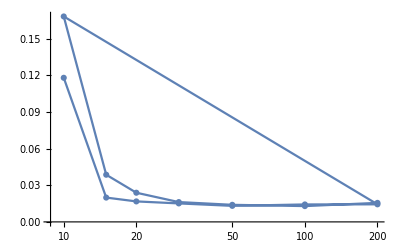

```mathematica
ls=SplitBy[ressum[[2;;]],#[[2]]&];
ls2={#[[1,2]],Mean[#[[All,7]]/#[[All,9]]]}&/@ls;
ListLogLinearPlot[ls2,PlotMarkers->Automatic,PlotRange->All,Joined->True]
```

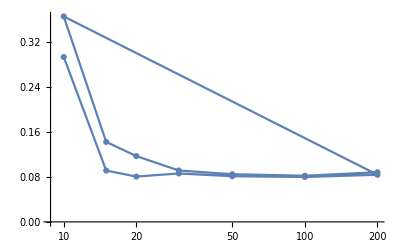

```mathematica
ls=SplitBy[ressum[[2;;]],#[[2]]&];
ls2={#[[1,2]],Mean[#[[All,-2]]]}&/@ls;
ListLogLinearPlot[ls2,PlotMarkers->Automatic,PlotRange->All,Joined->True]
```